```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.3;
ωmax=3.7;
Amin=0.0;
Amax=0.08;
Npoints=100;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]
M=32;
M2=3;
A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*2*n+I*ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1-(-1)^i*Δ)*Cos[q/2]*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]
A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-2*κ*(1-(-1)^i*Δ)*Cos[q/2]*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
κ=1;
η=0.1;
```

/Users/zack/Documents/oscillators/anharmonic

## Direct simulations

```mathematica
filebase="data/anharmonicsupercritical";
Import[filebase<>"out.dat"][[1]]
```

{./pendula.py,--filebase,data/anharmonicsupercritical,--num,1000,--cycles,5000,--noisestep,5,--dt,0.25,--frequency,3.44,--amplitude,0.045,--noise,0.01}

```mathematica
filebase="data/subharmonicsubcritical";
Import[filebase<>"out.dat"][[1]]
{M,dt,freq,amp,epsilon,order,response,wavenumber}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Dimensions[dat]
norms=Total/@(Abs[dat]^2)/M;
min=Quantile[Flatten[dat[[All,2;;M;;2]]],0.01]
max=Quantile[Flatten[dat[[All,2;;M;;2]]],0.99]
cf[x_]:=ColorData["TemperatureMap"][(x-min)/(max-min)];
dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs,power}=Partition[dat2,Length[dat2]/2];
Grid[{{rasterizeBackground[ListLogPlot[{Transpose[{freqs,power}]},PlotRange->{{0,3},All},PlotStyle->Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-5,2,2}],Table[{10^i,""},{i,-5,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,3,0.5}],Table[{i,""},{i,0,3,0.5}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]],rasterizeBackground[ListPlot[Transpose[{Range[Length[dat]]*dt,dat[[1;;-1;;1,2]]}],PlotRange->{-Pi,Pi},PlotStyle->Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameLabel->{t,Subscript[θ,1]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]],rasterizeBackground[ListPlot[dat[[-1,1;;M;;2]],PlotRange->{-Pi,Pi},PlotStyle->Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameLabel->{i,Subscript[θ,1]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]]}}]
{dNt,dNt2}=10*Round[1/(dt*Sort[{#,1-#}]&@freqs[[First@FirstPosition[power,Max[power]]]])]
Nt0=Mod[First@FirstPosition[dat,Max[dat[[-dNt;;-1,2;;M;;2]]]]-1,dNt]+1
Nt0=1
N2=Floor[20/dt]

Grid[{{rasterizeBackground[ListPlot[{Transpose[{Range[Length[Log[norms[[Nt0;;-1;;dNt]]]]]*dNt*dt,Log[norms[[Nt0;;-1;;dNt]]]/Log[10]}],Transpose[{Range[Length[Log[norms[[Nt0+dNt2;;-1;;dNt]]]]]*dNt*dt,Log[norms[[Nt0+dNt2;;-1;;dNt]]]/Log[10]}]},Joined->True,ImageSize->300,ImageSize->300,AspectRatio->1,PlotRange->All]],rasterizeBackground[ListPlot[dat[[Floor[Length[dat]/2];;-1,1;;2]],Axes->False,Frame->True,PlotRange->All,FrameLabel->{Subscript[ϕ,0],Subscript[ϕ,1]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{65,15},{65,10}}, ImageSize->350,AspectRatio->1]]}}]
p=Grid[{{rasterizeBackground[ListLogPlot[{Transpose[{freqs,power/(M*2*Pi)}]},PlotRange->{{0,3},All},PlotStyle->Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-5,2,2}],Table[{10^i,""},{i,-5,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,3,0.5}],Table[{i,""},{i,0,3,0.5}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]],rasterizeBackground[ListDensityPlot[dat[[Nt0;;-1;;dNt,2;;M+1;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,InterpolationOrder->0,FrameTicks->{{Table[{i,Round[i*dNt*dt]},{i,0,N[(Length[dat])/dNt],N[(Length[dat])/(5*dNt)]}],Table[{i,""},{i,0,N[(Length[dat])/dNt],N[(Length[dat])/(5*dNt)]}]},{Table[{i,i},{i,0,M/2,M/10}],Table[{i,""},{i,0,M/2,M/10}]}},FrameLabel->{i,t},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]]}}]
```

{./pendula.py,--filebase,data/subharmonicsubcritical,--num,1000,--cycles,5000,--noisestep,5,--dt,0.25,--frequency,3.9,--amplitude,0.019,--noise,0.01}

{1000,0.25,3.9,0.019,0.,0.104306,0.499925,3.16048}

{20000,2000}

-1.04952

1.04954

-Graphics- | -Graphics- | -Graphics-

{80,80}

8

1

80

-Graphics- | -Graphics-

-Graphics- | -Graphics-

```mathematica
min=Quantile[Flatten[dat[[All,2;;M;;2]]],0.01]
max=Quantile[Flatten[dat[[All,2;;M;;2]]],0.99]
cf[x_]:=ColorData["TemperatureMap"][(x-min)/(max-min)];
```

-1.04952

1.04954

```mathematica
Max[dat[[-dNt;;-1,2;;M;;2]]]
```

1.21649

```mathematica
Nt0=Mod[First@FirstPosition[dat,Max[dat[[-dNt;;-1,2;;M;;2]]]]-1,dNt]+1

p=Legended[rasterizeBackground[ListDensityPlot[(-1)^Range[M/2]*#&/@dat[[Nt0;;-1;;dNt,2;;M;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,InterpolationOrder->0,FrameTicks->{{Table[{i,Round[i*dNt*dt]},{i,0,N[(Length[dat])/dNt],N[(Length[dat])/(5*dNt)]}],Table[{i,""},{i,0,N[(Length[dat])/dNt],N[(Length[dat])/(5*dNt)]}]},{Table[{i,i},{i,0,M/2,M/10}],Table[{i,""},{i,0,M/2,M/10}]}},FrameLabel->{i,t},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]],Placed[BarLegend[{cf[#]&,{min,max}},LegendLabel->DisplayForm[RowBox[{Subscript[θ,i],"/",Subscript[θ,"max"]}]],LabelStyle->Directive[14,Black],LegendLayout->"Row"],Above]]
p=Export[filebase<>"patterns.pdf",p]
```

8

-Graphics-

data/subharmonicsubcriticalpatterns.pdf

```mathematica
p=rasterizeBackground[ListDensityPlot[(1)^Range[M/2]*#&/@dat[[Nt0;;-1;;dNt,2;;M;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,InterpolationOrder->0,FrameTicks->{{Table[{i,Round[i*dNt*dt]},{i,0,N[(Length[dat])/dNt],N[(Length[dat])/(5*dNt)]}],Table[{i,""},{i,0,N[(Length[dat])/dNt],N[(Length[dat])/(5*dNt)]}]},{Table[{i,i},{i,0,M/2,M/10}],Table[{i,""},{i,0,M/2,M/10}]}},FrameLabel->{i,t},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]]
Export[filebase<>"patterns.pdf",p]
```

-Graphics-

data/testpatterns.pdf

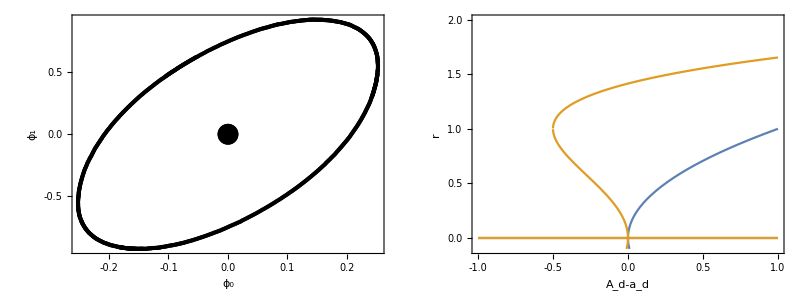

neimark.pdf

```mathematica
p=Grid[{{ListPlot[{dat[[Floor[Length[dat]/2];;Floor[Length[dat]/2]+20000;;20,1;;2]],{{0,0}}},Axes->False,Frame->True,PlotRange->All,FrameLabel->{Subscript[ϕ,0],Subscript[ϕ,1]},PlotStyle->{Directive[Black,PointSize[0.01]],Directive[Black,PointSize[0.05]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16], ImagePadding->{{65,15},{65,10}}, ImageSize->300, AspectRatio->2/3,FrameTicks->{Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{-1.0,-0.5,0.0,0.5,1.0}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{-0.2,-0.1,0.0,0.1,0.2}]}],Plot[{r/.Solve[r-1/ϵ*r^3==0,r],r/.Solve[r+1/ϵ*r^3-0.5/ϵ*r^5==0,r]},{ϵ,-1,1},PlotRange->{{-1,1},{-0.1,2}},Axes->False,Frame->True,FrameLabel->{Subscript[A,d]-Subscript[a,d],r},LabelStyle->Directive[16,Black],FrameStyle->Directive[AbsoluteThickness[2],Black],ImagePadding->{{65,15},{65,10}},ImagePadding->{{65,15},{65,10}}, ImageSize->300, AspectRatio->2/3,FrameTicks->{Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{0.0,0.5,1.0,1.5,2.0}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{-1.0,-0.5,0.0,0.5,1.0}]}]}}]
Export["neimark.pdf",p]
```

```mathematica
Table[(0.1*n/15)^2/(2*0.1),{n,0,15}]
```

{0.,0.000222222,0.000888889,0.002,0.00355556,0.00555556,0.008,0.0108889,0.0142222,0.018,0.0222222,0.0268889,0.032,0.0375556,0.0435556,0.05}

## Fig 5

{3577,7165}

{6686,3338}

{3387,6787}

-Graphics-

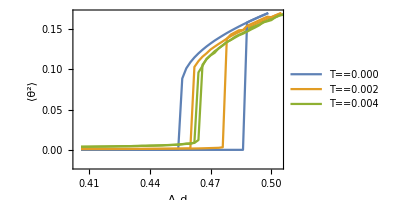
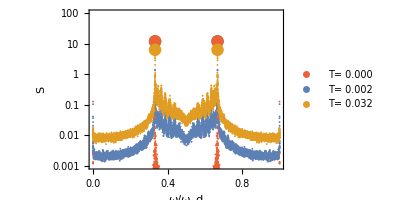
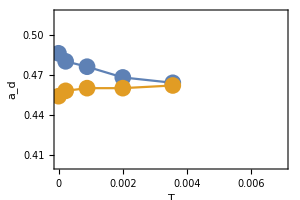
-Graphics- | -Graphics- | -Graphics- | -Graphics-

critical2.pdf

```mathematica
Monitor[vals0=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_0out.dat"][[3]],{j,0,50},{i,0,10}];,{i,j}]
Monitor[vals1=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_1out.dat"][[3]],{j,0,50},{i,0,10}];,{i,j}]

seed=1;
filebase="data/noisy/0_"<>ToString[seed];
dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs1,power1}=Partition[dat2,Length[dat2]/2];
T1=ToExpression[Import[filebase<>"out.dat"][[1,17]]]^2/(2*0.1);
filebase="data/noisy/3_"<>ToString[seed];
dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs2,power2}=Partition[dat2,Length[dat2]/2];
T2=ToExpression[Import[filebase<>"out.dat"][[1,17]]]^2/(2*0.1);
filebase="data/noisy/12_"<>ToString[seed];
dat3=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs3,power3}=Partition[dat3,Length[dat3]/2];
T3=ToExpression[Import[filebase<>"out.dat"][[1,17]]]^2/(2*0.1);
p0=Legended[ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}],Transpose[{freqs3,power3}]},PlotRange->{{0,1.0},{10^-3,10^2}},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[2]]]},Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-3,2,2}],Table[{10^i,""},{i,-3,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}}],Placed[PointLegend[{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},{DisplayForm[RowBox[{T,"=",PaddedForm[T1,{2,3}]}]],DisplayForm[RowBox[{T,"=",PaddedForm[T2,{2,3}]}]],DisplayForm[RowBox[{T,"=",PaddedForm[T3,{2,3}]}]]},LabelStyle->Directive[12]],{0.15,0.7}]];
m2={#,Length[power2]-#+2}&@(First@FirstPosition[power2,Max[power2]])
m1={#,Length[power1]-#+2}&@(First@FirstPosition[power1,Max[power1]])
m3={#,Length[power3]-#+2}&@(First@FirstPosition[power3,Max[power3]])
p1=ListLogPlot[{Transpose[{freqs2,power2}][[m2]],Transpose[{freqs1,power1}][[m1]],Transpose[{freqs3,power3}][[m3]]},PlotStyle->{Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.03],ColorData[97,"ColorList"][[4]]],Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]}];

vals=Table[filebase="data/noisy/"<>ToString[n]<>"_"<>ToString[m];dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];{freqs1,power1}=Partition[dat2,Length[dat2]/2];
{0.1*n/15/(2*0.1),Max[power1]},{n,0,15},{m,0,15}];
means=Mean/@vals;
vars=(StandardDeviation/@vals);
p2=ListPlot[Table[{means[[i,1]],Around[means[[i,2]],vars[[i,2]]]},{i,1,Length[means]}],Joined->True,LabelStyle->Directive[12,Black],Axes->False,Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],FrameLabel->{T,Subscript[S,"max"]},AspectRatio->1,ImageSize->125,FrameTicks->{Transpose[{{#,#},{#,""}}&/@{0,6,12}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{0,0.2,0.4}]}];
vals=Table[filebase="data/noisy/"<>ToString[n]<>"_"<>ToString[m];dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];{freqs1,power1}=Partition[dat2,Length[dat2]/2];
{(0.1*n/15)^2/(2*0.1),Max[power1]},{n,0,15},{m,0,15}];
means=Mean/@vals;
vars=(StandardDeviation/@vals);
p2=ListPlot[Table[{Log[means[[i,1]]]/Log[10],Around[means[[i,2]],vars[[i,2]]]},{i,1,Length[means]}][[2;;-1]],Joined->True,LabelStyle->Directive[12,Black],Axes->False,Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],FrameLabel->{T,Subscript[S,"max"]},AspectRatio->1,ImageSize->125,FrameTicks->{Transpose[{{#,#},{#,""}}&/@{0,6,12}],Transpose[{{#,HoldForm["10"^(DisplayForm[RowBox[{#}]])]},{#,""}}&/@{-3,-2,0}]}]
p3=Grid[{{Show[p0,p1],p2}}];
p=Grid[{{Show[ListPlot[Table[vals1[[All,i,1]],{i,1,5,2}],Joined->True,PlotRange->{{0,50},{-0.02,0.17}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{Subscript["A",d],AngleBracket[θ^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.15,0.05}],Table[{i,""},{i,0,0.15,0.05}]},{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]}},PlotLegends->Placed[{T=="0.000",T=="0.002",T=="0.004"},{0.25,0.5}]],ListPlot[Table[vals0[[All,i,1]],{i,1,5,2}],Joined->True,PlotRange->{{0,50},{-0.02,0.17}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{a,AngleBracket[θ^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.15,0.05}],Table[{i,""},{i,0,0.15,0.05}]},{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]}}]],p3,
Show[ListPlot[{Transpose[{ts[[1;;5]],Table[First@FirstPosition[Differences[vals0[[All,i,1]]],Max[Differences[vals0[[All,i,1]]]]],{i,1,5}]}],
Transpose[{ts[[1;;5]],Table[First@FirstPosition[Differences[vals1[[All,i,1]]],Max[Differences[vals1[[All,i,1]]]]],{i,1,5}]}]},Joined->True,PlotRange->{{0,0.007},{-1,56}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{T,Subscript[a,d]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]},{{0,0.002,0.004,0.006},{{0,""},{0.002,""},{0.004,""},{0.006,""}}}}],ListPlot[{Transpose[{ts[[1;;5]],Table[First@FirstPosition[Differences[vals0[[All,i,1]]],Max[Differences[vals0[[All,i,1]]]]],{i,1,5}]}],
Transpose[{ts[[1;;5]],Table[First@FirstPosition[Differences[vals1[[All,i,1]]],Max[Differences[vals1[[All,i,1]]]]],{i,1,5}]}]},Joined->False,PlotStyle->Directive[PointSize[0.04]]]]}}]
Export["critical2.pdf",p]
```

```mathematica
Import[filebase<>"out.dat"]
```

{{./pendula.py,--seed,16,--verbose,0,--initcycle,0,--cycles,16000,--outcycle,5000,--dt,1.,--amplitude,0.05,--noise,0.0999999999999999999,--noisestep,20,--filebase,data/noisy/15_15},{32,1.,3.4,0.05,0.,0.151082,0.336722,0.418879},{runtime:,820.738}}

```mathematica
Import[filebase<>"out.dat"][[1,17]]
```

0.0999999999999999999

```mathematica
ToExpression[Import[filebase<>"out.dat"][[1,19]]]^2/(2*0.1)
```

100.

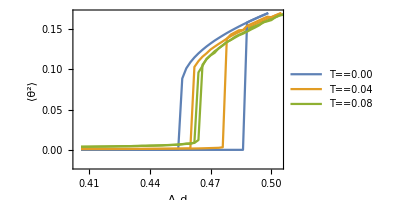

```mathematica
Show[ListPlot[Table[vals1[[All,i,1]],{i,1,5,2}],Joined->True,PlotRange->{{0,50},{-0.02,0.17}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{Subscript["A",d],AngleBracket[θ^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.15,0.05}],Table[{i,""},{i,0,0.15,0.05}]},{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]}},PlotLegends->Placed[{T=="0.00",T=="0.04",T=="0.08"},{0.25,0.5}]],ListPlot[Table[vals0[[All,i,1]],{i,1,5,2}],Joined->True,PlotRange->{{0,50},{-0.02,0.17}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{a,AngleBracket[θ^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.15,0.05}],Table[{i,""},{i,0,0.15,0.05}]},{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]}}]]
```

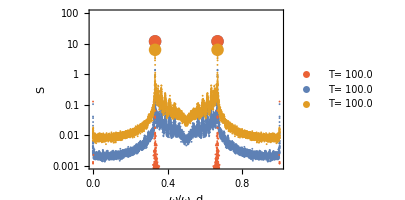
-Graphics- | -Graphics-

```mathematica
vals=Table[filebase="data/noisy/"<>ToString[n]<>"_"<>ToString[m];dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];{freqs1,power1}=Partition[dat2,Length[dat2]/2];
{(0.1*n/15)^2/(2*0.1),Max[power1]},{n,0,15},{m,0,15}];
means=Mean/@vals;
vars=(StandardDeviation/@vals);
p2=ListPlot[Table[{means[[i,1]],Around[means[[i,2]],vars[[i,2]]]},{i,1,Length[means]}],Joined->True,LabelStyle->Directive[12,Black],Axes->False,Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],FrameLabel->{T,Subscript[S,"max"]},AspectRatio->1,ImageSize->125,FrameTicks->{Transpose[{{#,#},{#,""}}&/@{0,6,12}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{0,0.2,0.4}]}];
p3=Grid[{{Show[p0,p1],p2}}]
```

{{Indeterminate,12.140.27},{-3.65321,11.970.23},{-3.05115,12.080.16},{-2.69897,11.830.13},{-2.44909,11.590.33},{-2.25527,11.260.23},{-2.09691,10.80.5},{-1.96302,10.20.9},{-1.84703,9.60.9},{-1.74473,9.11.4},{-1.65321,7.81.2},{-1.57043,6.91.5},{-1.49485,5.81.4},{-1.42533,4.40.9},{-1.36096,2.90.6},{-1.30103,2.20.4}}

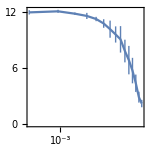

```mathematica
Table[{Log[means[[i,1]]]/Log[10],Around[means[[i,2]],vars[[i,2]]]},{i,1,Length[means]}]
```

```mathematica
T
```

```mathematica
Monitor[test=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_0out.dat"],{j,0,50},{i,0,10}];,{i,j}]
```

```mathematica
0.04/(2*0.1)
```

0.2

```mathematica
0.04^2/(2*0.1)
```

0.008

```mathematica
test[[All,-1]]
```

{{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.04,--noise,0.04,--noisestep,10,--filebase,data/noise/10_0_0},{100,3.4,0.04,0.5,0.1,0.,0.5,50000.,1,10},{0.028567,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2234.06}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0402,--noise,0.04,--noisestep,10,--filebase,data/noise/10_1_0},{100,3.4,0.0402,0.5,0.1,0.,0.5,50000.,1,10},{0.029248,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2173.89}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0404,--noise,0.04,--noisestep,10,--filebase,data/noise/10_2_0},{100,3.4,0.0404,0.5,0.1,0.,0.5,50000.,1,10},{0.029625,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2173.93}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0406,--noise,0.04,--noisestep,10,--filebase,data/noise/10_3_0},{100,3.4,0.0406,0.5,0.1,0.,0.5,50000.,1,10},{0.030219,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2290.81}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0408,--noise,0.04,--noisestep,10,--filebase,data/noise/10_4_0},{100,3.4,0.0408,0.5,0.1,0.,0.5,50000.,1,10},{0.031295,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2230.98}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.041,--noise,0.04,--noisestep,10,--filebase,data/noise/10_5_0},{100,3.4,0.041,0.5,0.1,0.,0.5,50000.,1,10},{0.03201,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2184.36}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0412,--noise,0.04,--noisestep,10,--filebase,data/noise/10_6_0},{100,3.4,0.0412,0.5,0.1,0.,0.5,50000.,1,10},{0.033269,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2133.26}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0414,--noise,0.04,--noisestep,10,--filebase,data/noise/10_7_0},{100,3.4,0.0414,0.5,0.1,0.,0.5,50000.,1,10},{0.033491,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2204.89}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0416,--noise,0.04,--noisestep,10,--filebase,data/noise/10_8_0},{100,3.4,0.0416,0.5,0.1,0.,0.5,50000.,1,10},{0.034705,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2242.87}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0418,--noise,0.04,--noisestep,10,--filebase,data/noise/10_9_0},{100,3.4,0.0418,0.5,0.1,0.,0.5,50000.,1,10},{0.035698,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2124.92}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.042,--noise,0.04,--noisestep,10,--filebase,data/noise/10_10_0},{100,3.4,0.042,0.5,0.1,0.,0.5,50000.,1,10},{0.038026,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2165.48}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0422,--noise,0.04,--noisestep,10,--filebase,data/noise/10_11_0},{100,3.4,0.0422,0.5,0.1,0.,0.5,50000.,1,10},{0.039178,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2392.08}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0424,--noise,0.04,--noisestep,10,--filebase,data/noise/10_12_0},{100,3.4,0.0424,0.5,0.1,0.,0.5,50000.,1,10},{0.039689,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2335.53}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0426,--noise,0.04,--noisestep,10,--filebase,data/noise/10_13_0},{100,3.4,0.0426,0.5,0.1,0.,0.5,50000.,1,10},{0.043702,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2232.45}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0428,--noise,0.04,--noisestep,10,--filebase,data/noise/10_14_0},{100,3.4,0.0428,0.5,0.1,0.,0.5,50000.,1,10},{0.04373,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2269.8}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.043,--noise,0.04,--noisestep,10,--filebase,data/noise/10_15_0},{100,3.4,0.043,0.5,0.1,0.,0.5,50000.,1,10},{0.046763,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2110.62}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0432,--noise,0.04,--noisestep,10,--filebase,data/noise/10_16_0},{100,3.4,0.0432,0.5,0.1,0.,0.5,50000.,1,10},{0.048713,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2171.1}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0434,--noise,0.04,--noisestep,10,--filebase,data/noise/10_17_0},{100,3.4,0.0434,0.5,0.1,0.,0.5,50000.,1,10},{0.050586,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2142.7}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0436,--noise,0.04,--noisestep,10,--filebase,data/noise/10_18_0},{100,3.4,0.0436,0.5,0.1,0.,0.5,50000.,1,10},{0.054266,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2032.47}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0438,--noise,0.04,--noisestep,10,--filebase,data/noise/10_19_0},{100,3.4,0.0438,0.5,0.1,0.,0.5,50000.,1,10},{0.057186,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2109.19}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.044,--noise,0.04,--noisestep,10,--filebase,data/noise/10_20_0},{100,3.4,0.044,0.5,0.1,0.,0.5,50000.,1,10},{0.058974,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2089.93}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0442,--noise,0.04,--noisestep,10,--filebase,data/noise/10_21_0},{100,3.4,0.0442,0.5,0.1,0.,0.5,50000.,1,10},{0.059411,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2137.31}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0444,--noise,0.04,--noisestep,10,--filebase,data/noise/10_22_0},{100,3.4,0.0444,0.5,0.1,0.,0.5,50000.,1,10},{0.063539,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2126.58}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0446,--noise,0.04,--noisestep,10,--filebase,data/noise/10_23_0},{100,3.4,0.0446,0.5,0.1,0.,0.5,50000.,1,10},{0.065455,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2189.}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0448,--noise,0.04,--noisestep,10,--filebase,data/noise/10_24_0},{100,3.4,0.0448,0.5,0.1,0.,0.5,50000.,1,10},{0.068492,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2129.72}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.045,--noise,0.04,--noisestep,10,--filebase,data/noise/10_25_0},{100,3.4,0.045,0.5,0.1,0.,0.5,50000.,1,10},{0.072305,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2076.83}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0452,--noise,0.04,--noisestep,10,--filebase,data/noise/10_26_0},{100,3.4,0.0452,0.5,0.1,0.,0.5,50000.,1,10},{0.074942,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2360.02}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0454,--noise,0.04,--noisestep,10,--filebase,data/noise/10_27_0},{100,3.4,0.0454,0.5,0.1,0.,0.5,50000.,1,10},{0.079323,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2024.45}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0456,--noise,0.04,--noisestep,10,--filebase,data/noise/10_28_0},{100,3.4,0.0456,0.5,0.1,0.,0.5,50000.,1,10},{0.077525,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1950.04}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0458,--noise,0.04,--noisestep,10,--filebase,data/noise/10_29_0},{100,3.4,0.0458,0.5,0.1,0.,0.5,50000.,1,10},{0.082046,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2159.01}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.046,--noise,0.04,--noisestep,10,--filebase,data/noise/10_30_0},{100,3.4,0.046,0.5,0.1,0.,0.5,50000.,1,10},{0.085154,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2213.53}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0462,--noise,0.04,--noisestep,10,--filebase,data/noise/10_31_0},{100,3.4,0.0462,0.5,0.1,0.,0.5,50000.,1,10},{0.088089,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2001.43}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0464,--noise,0.04,--noisestep,10,--filebase,data/noise/10_32_0},{100,3.4,0.0464,0.5,0.1,0.,0.5,50000.,1,10},{0.090199,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1943.68}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0466,--noise,0.04,--noisestep,10,--filebase,data/noise/10_33_0},{100,3.4,0.0466,0.5,0.1,0.,0.5,50000.,1,10},{0.093075,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2022.99}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0468,--noise,0.04,--noisestep,10,--filebase,data/noise/10_34_0},{100,3.4,0.0468,0.5,0.1,0.,0.5,50000.,1,10},{0.094465,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1945.9}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.047,--noise,0.04,--noisestep,10,--filebase,data/noise/10_35_0},{100,3.4,0.047,0.5,0.1,0.,0.5,50000.,1,10},{0.095458,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1899.19}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0472,--noise,0.04,--noisestep,10,--filebase,data/noise/10_36_0},{100,3.4,0.0472,0.5,0.1,0.,0.5,50000.,1,10},{0.09733,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2031.95}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0474,--noise,0.04,--noisestep,10,--filebase,data/noise/10_37_0},{100,3.4,0.0474,0.5,0.1,0.,0.5,50000.,1,10},{0.100277,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1973.71}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0476,--noise,0.04,--noisestep,10,--filebase,data/noise/10_38_0},{100,3.4,0.0476,0.5,0.1,0.,0.5,50000.,1,10},{0.102886,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1972.33}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0478,--noise,0.04,--noisestep,10,--filebase,data/noise/10_39_0},{100,3.4,0.0478,0.5,0.1,0.,0.5,50000.,1,10},{0.102764,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1895.47}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.048,--noise,0.04,--noisestep,10,--filebase,data/noise/10_40_0},{100,3.4,0.048,0.5,0.1,0.,0.5,50000.,1,10},{0.1058,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1976.53}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0482,--noise,0.04,--noisestep,10,--filebase,data/noise/10_41_0},{100,3.4,0.0482,0.5,0.1,0.,0.5,50000.,1,10},{0.107561,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2324.61}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0484,--noise,0.04,--noisestep,10,--filebase,data/noise/10_42_0},{100,3.4,0.0484,0.5,0.1,0.,0.5,50000.,1,10},{0.110651,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1887.57}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0486,--noise,0.04,--noisestep,10,--filebase,data/noise/10_43_0},{100,3.4,0.0486,0.5,0.1,0.,0.5,50000.,1,10},{0.111366,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1997.79}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0488,--noise,0.04,--noisestep,10,--filebase,data/noise/10_44_0},{100,3.4,0.0488,0.5,0.1,0.,0.5,50000.,1,10},{0.113591,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1909.91}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.049,--noise,0.04,--noisestep,10,--filebase,data/noise/10_45_0},{100,3.4,0.049,0.5,0.1,0.,0.5,50000.,1,10},{0.11539,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2014.48}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0492,--noise,0.04,--noisestep,10,--filebase,data/noise/10_46_0},{100,3.4,0.0492,0.5,0.1,0.,0.5,50000.,1,10},{0.115601,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,2025.62}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0494,--noise,0.04,--noisestep,10,--filebase,data/noise/10_47_0},{100,3.4,0.0494,0.5,0.1,0.,0.5,50000.,1,10},{0.117536,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1879.95}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0496,--noise,0.04,--noisestep,10,--filebase,data/noise/10_48_0},{100,3.4,0.0496,0.5,0.1,0.,0.5,50000.,1,10},{0.11873,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1990.05}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.0498,--noise,0.04,--noisestep,10,--filebase,data/noise/10_49_0},{100,3.4,0.0498,0.5,0.1,0.,0.5,50000.,1,10},{0.121076,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1877.45}},{{./pendula.py,--verbose,0,--num,100,--initcycle,10000,--cycles,50000,--outcycle,40000,--dt,0.5,--initamplitude,0.04,--amplitude,0.05,--noise,0.04,--noisestep,10,--filebase,data/noise/10_50_0},{100,3.4,0.05,0.5,0.1,0.,0.5,50000.,1,10},{0.122927,0.},{1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5,1.5,0.5},{runtime:,1909.6}}}

```mathematica
Monitor[vals0=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_0out.dat"][[3]],{j,0,50},{i,0,10}];,{i,j}]
Monitor[vals1=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_1out.dat"][[3]],{j,0,50},{i,0,10}];,{i,j}]
```

```mathematica
vals1[[1]]
```

{{0.,0.},{0.000231,0.},{0.000931,0.},{0.002127,0.},{0.003809,0.},{0.006116,0.},{0.008976,0.},{0.012464,0.},{0.016916,0.},{0.022049,0.},{0.028431,0.}}

```mathematica
Table[{i,PaddedForm[0.0+(0.04-0.0)/(0.1*2)*(i-1)/10,{3,2}]},{i,1,11,2}]
```

{{1, 0.00},{3, 0.04},{5, 0.08},{7, 0.12},{9, 0.16},{11, 0.20}}

{4724,9461}

{4809,9634}

{4908,9836}

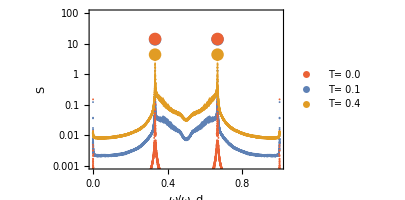
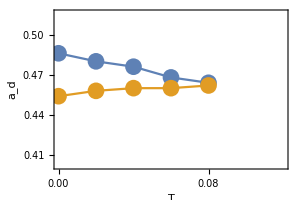
-Graphics- | -Graphics- | -Graphics- | -Graphics-

critical2.pdf

```mathematica
Monitor[vals0=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_0out.dat"][[3]],{j,0,50},{i,0,10}];,{i,j}]
Monitor[vals1=Table[Import["data/noise/"<>ToString[i]<>"_"<>ToString[j]<>"_1out.dat"][[3]],{j,0,50},{i,0,10}];,{i,j}]
seed=1;
filebase="data/noisy2/0_"<>ToString[seed];
dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs1,power1}=Partition[dat2,Length[dat2]/2];
T1=ToExpression[Import[filebase<>"out.dat"][[1,19]]]/(2*0.1);
filebase="data/noisy2/3_"<>ToString[seed];
dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs2,power2}=Partition[dat2,Length[dat2]/2];
T2=ToExpression[Import[filebase<>"out.dat"][[1,19]]]/(2*0.1);
filebase="data/noisy2/12_"<>ToString[seed];
dat3=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];
{freqs3,power3}=Partition[dat3,Length[dat3]/2];
T3=ToExpression[Import[filebase<>"out.dat"][[1,19]]]/(2*0.1);
p0=Legended[ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}],Transpose[{freqs3,power3}]},PlotRange->{{0,1.0},{10^-3,10^2}},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[2]]]},Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-3,2,2}],Table[{10^i,""},{i,-3,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}}],Placed[PointLegend[{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]],ColorData[97,"ColorList"][[2]]},{DisplayForm[RowBox[{T,"=",PaddedForm[T1,{2,1}]}]],DisplayForm[RowBox[{T,"=",PaddedForm[T2,{2,1}]}]],DisplayForm[RowBox[{T,"=",PaddedForm[T3,{2,1}]}]]},LabelStyle->Directive[12]],{0.15,0.7}]];
m2={#,Length[power2]-#+2}&@(First@FirstPosition[power2,Max[power2]])
m1={#,Length[power1]-#+2}&@(First@FirstPosition[power1,Max[power1]])
m3={#,Length[power3]-#+2}&@(First@FirstPosition[power3,Max[power3]])
p1=ListLogPlot[{Transpose[{freqs2,power2}][[m2]],Transpose[{freqs1,power1}][[m1]],Transpose[{freqs3,power3}][[m3]]},PlotStyle->{Directive[PointSize[0.03],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.03],ColorData[97,"ColorList"][[4]]],Directive[PointSize[0.03],ColorData[97,"ColorList"][[2]]]}];

vals=Table[filebase="data/noisy2/"<>ToString[n]<>"_"<>ToString[m];dat2=BinaryReadList[filebase<>"power.npy","Real64"][[17;;-1]];{freqs1,power1}=Partition[dat2,Length[dat2]/2];
{0.1*n/15/(2*0.1),Max[power1]},{n,0,15},{m,0,15}];
means=Mean/@vals;
vars=(StandardDeviation/@vals);
p2=ListPlot[Table[{means[[i,1]],Around[means[[i,2]],vars[[i,2]]]},{i,1,Length[means]}],Joined->True,LabelStyle->Directive[12,Black],Axes->False,Frame->True,FrameStyle->Directive[AbsoluteThickness[2],Black],FrameLabel->{T,Subscript[S,"max"]},AspectRatio->1,ImageSize->125,FrameTicks->{Transpose[{{#,#},{#,""}}&/@{0,6,12}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{0,0.2,0.4}]}];
p3=Grid[{{Show[p0,p1],p2}}];
p=Grid[{{Show[ListPlot[Table[vals1[[All,i,1]],{i,1,5,2}],Joined->True,PlotRange->{{0,50},{-0.02,0.17}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{Subscript["A",d],AngleBracket[θ^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.15,0.05}],Table[{i,""},{i,0,0.15,0.05}]},{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]}},PlotLegends->Placed[{T=="0.00",T=="0.04",T=="0.08"},{0.25,0.5}]],ListPlot[Table[vals0[[All,i,1]],{i,1,5,2}],Joined->True,PlotRange->{{0,50},{-0.02,0.17}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{a,AngleBracket[θ^2]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.15,0.05}],Table[{i,""},{i,0,0.15,0.05}]},{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]}}]],p3,
Show[ListPlot[{Table[First@FirstPosition[Differences[vals0[[All,i,1]]],Max[Differences[vals0[[All,i,1]]]]],{i,1,5}],
Table[First@FirstPosition[Differences[vals1[[All,i,1]]],Max[Differences[vals1[[All,i,1]]]]],{i,1,5}]},Joined->True,PlotRange->{{1,7},{-1,56}},AspectRatio->2/3,ImageSize->300,ImagePadding->{{75,25},{55,15}},Axes->False,Frame->True,FrameLabel->{T,Subscript[a,d]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{{Table[{i,PaddedForm[0.4+(0.5-0.4)*i/50,{2,2}]},{i,3,50,15}],Table[{i,""},{i,3,50,15}]},{Table[{i,PaddedForm[0.0+(0.04-0.0)/(0.1*2)*(i-1)/10,{3,2}]},{i,1,11,2}],Table[{i,""},{i,1,11,2}]}}],ListPlot[{Table[First@FirstPosition[Differences[vals0[[All,i,1]]],Max[Differences[vals0[[All,i,1]]]]],{i,1,5}],
Table[First@FirstPosition[Differences[vals1[[All,i,1]]],Max[Differences[vals1[[All,i,1]]]]],{i,1,5}]},Joined->False,PlotStyle->Directive[PointSize[0.04]]]]}}]
Export["critical2.pdf",p]
```

## Defect dynamics

```mathematica
filebase="data/large1";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Dimensions[dat]

Manipulate[ListPlot[{dat[[m,1;;M;;2]],dat[[m,2;;M;;2]]},PlotRange->{-Pi,Pi},Joined->True],{m,1,Length[dat],1}]
```

{1000,3.4,0.05,0.2,0.1,0.,0.5,5000.,1,1}

{25000,2000}

```mathematica
max=Max[dat]
min=Min[dat]
cf[x_]:=ColorData["TemperatureMap"][(x-min)/(max-min)];
Grid[{{rasterizeBackground[ListDensityPlot[dat[[1;;-1;;20,1;;M;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0,ImageSize->300,AspectRatio->1]],rasterizeBackground[ListDensityPlot[dat[[1;;-1;;20,2;;M;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0,ImageSize->300,AspectRatio->1]]}}]
```

0.234853

-0.234115

-Graphics- | -Graphics-

```mathematica
Grid[{{rasterizeBackground[ListDensityPlot[dat[[1;;-1;;3,1;;M;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0,ImageSize->300,AspectRatio->1]],rasterizeBackground[ListDensityPlot[dat[[1;;-1;;3,2;;M;;2]],PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0,ImageSize->300,AspectRatio->1]]}}]
```

-Graphics- | -Graphics-

```mathematica
n0=100;
n2=Position[Differences[Sign[Differences[Total[Abs[#-dat[[n0/dt]]]^2]&/@dat]]],2][[-1,1]];
power=Abs[Fourier[dat[[n0/dt;;n2,1]]]];
freqs=Range[Length[dat[[n0/dt;;n2,1]]]]/(Length[dat[[n0/dt+1;;n2,1]]]*dt);
rasterizeBackground[ListLogPlot[{Transpose[{freqs,power}]},PlotRange->{{0,3},All},PlotStyle->Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-5,2,2}],Table[{10^i,""},{i,-5,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,3,0.5}],Table[{i,""},{i,0,3,0.5}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1]]
```

-Graphics-

```mathematica
dt
```

1.

```mathematica
freqs[[Flatten[Position[power,Max[power]]]]]
```

{0.333129,0.667484}

```mathematica
AbsoluteTiming[Monitor[plots=Table[ListPlot[{dat[[All,1;;M;;2]],Mod[dat[[m,2;;M;;2]]+Pi,2*Pi]-Pi},PlotRange->{-Pi,Pi},Joined->True],{m,1,200,1}];,N[m/200]]]
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots[[n]]], {n,1,Length[plots]}]]
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

{36.6007,Null}

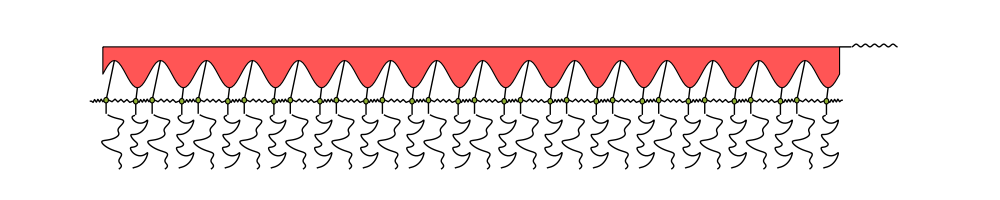

/Users/zack/Documents/oscillators/anharmonic/data/test2animation/4/

{206.981,Null}

```mathematica
Δ=0.5;
dx=1;
filebase="data/test2";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
n0=Max[1,Length[dat]-1000];
Clear[a];
Clear[t];
Clear[m]
M=32;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],
Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],
Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
p0
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

## Schematic and dispersion

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

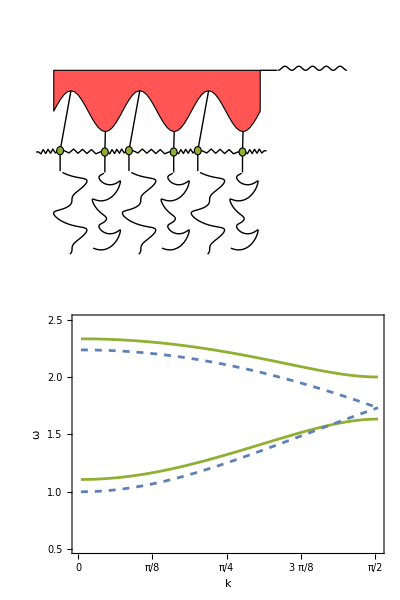

fig1.pdf

```mathematica
filebase="data/anharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
dx=1;
M=6;
n=Length[dat];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->500,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}];
p1=Show[ListPlot[Transpose[Table[Re[ω/.dispersion/.Δ->0.5],{q,0,Pi,Pi/100}]],Joined->True,PlotRange->{0.5,2.5},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{25,DisplayForm[RowBox[{"π","/",8}]]},{50,DisplayForm[RowBox[{"π","/",4}]]},{75,DisplayForm[RowBox[{3"π","/",8}]]},{100,DisplayForm[RowBox[{"π","/",2}]]}},Table[{i,""},{i,0,100,25}]}},Axes->False,Frame->True,FrameLabel->{k,ω},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImageSize->350,PlotStyle->Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],AspectRatio->1/2],
ListPlot[Transpose[Table[Re[ω/.dispersion/.Δ->0.0],{q,0,Pi,Pi/100}]],Joined->True,PlotRange->{0,3},Axes->False,Frame->True,FrameLabel->{k,ω},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImageSize->350,PlotStyle->Directive[Dashed,AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]],AspectRatio->1/3]];
p=Grid[{{p0},{p1}}]
Export["fig1.pdf",p]
```

## Floquet exponents

### Specific parameters

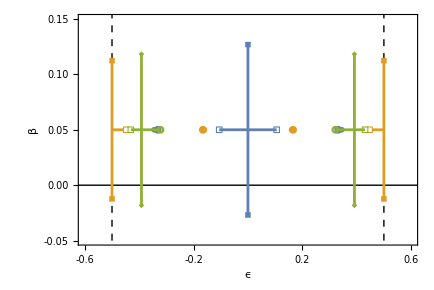

```mathematica
Clear[ω]
ωd=1.0;
Δ=0.5;
amin=0.01;
amax=0.8;
q=0;
markersize=0.03;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]],PlotMarkers->{Graphics[{Circle[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[1]]], White, Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Disk[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}}]];
ωd=2.0;
amin=0.01;
amax=0.12;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p2=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[5;;6]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],White,Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Circle[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
ωd=1.63;
amin=0.0;
amax=0.35;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p3=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[3]]],White,Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Circle[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[2^(1/2)*{{0,markersize},{markersize,0},{0,-markersize},{-markersize,0}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[2^(1/2)*{{0,markersize},{markersize,0},{0,-markersize},{-markersize,0}}]},PlotRange->{{-1,1},{-1,1}}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p1=Show[p1,p2,p3,AspectRatio->2/3,ImageSize->435,ImagePadding->{{75,15},{75,15}},FrameTicks->{{Table[{i,PaddedForm[N[i],{3,2}]},{i,-0.05,0.15,0.05}],Table[{i,""},{i,-0.05,0.15,0.05}]},{Table[{i,PaddedForm[N[i],{2,1}]},{i,-6/10,6/10,2/10}],Table[{i,""},{i,-6/10,6/10,2/10}]}}]
```

```mathematica
ωd=3.4;
AbsoluteTiming[Monitor[test1=Table[Eigenvalues[{A4[ωd,0,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test2=Table[Eigenvalues[{A4[ωd,Δ,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test3=Table[Eigenvalues[{A4[ωd,0,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test4=Table[Eigenvalues[{A4[ωd,Δ,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
```

{1.56424,Null}

{1.59963,Null}

{1.60508,Null}

{1.64383,Null}

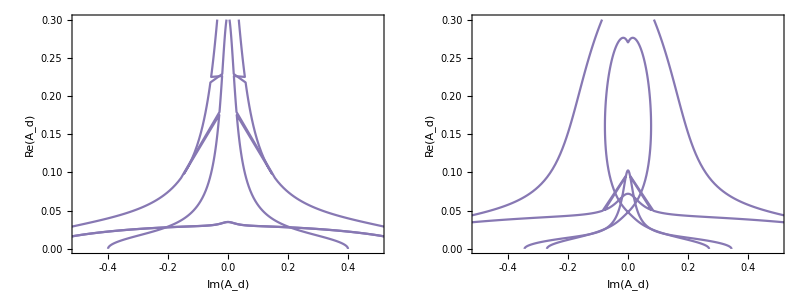
-Graphics-
-Graphics-

fig4.pdf

```mathematica
p1=Show[p1,p2,p3,AspectRatio->2/3,ImageSize->435,ImagePadding->{{75,15},{75,15}},FrameTicks->{{Table[{i,PaddedForm[N[i],{3,2}]},{i,-0.05,0.15,0.05}],Table[{i,""},{i,-0.05,0.15,0.05}]},{Table[{i,PaddedForm[N[i],{2,1}]},{i,-6/10,6/10,2/10}],Table[{i,""},{i,-6/10,6/10,2/10}]}}]
p2=Grid[{{Show[ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test1[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]],ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test3[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]]],Show[ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test2[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]],ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test4[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]]]}}];
p=Grid[{{p1},{p2}}]
Export["fig4.pdf",p]
```

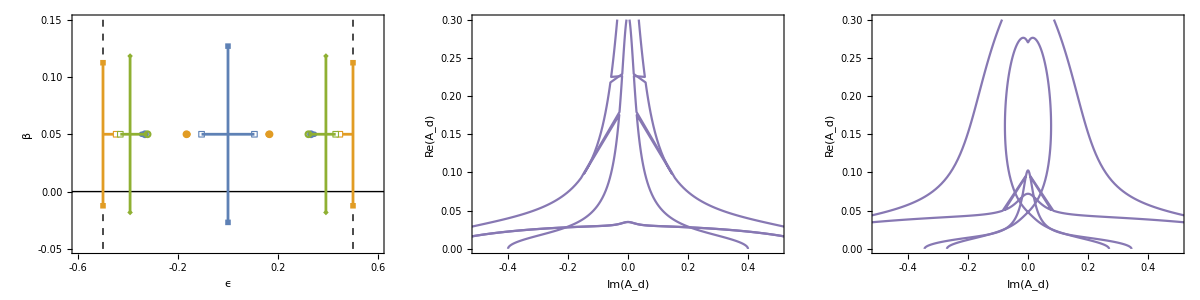

fig4.pdf

```mathematica
Clear[ω]
ωd=1.0;
Δ=0.5;
amin=0.01;
amax=0.8;
q=0;
markersize=0.03;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]],PlotMarkers->{Graphics[{Circle[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[1]]], White, Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Disk[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}}]];
ωd=2.0;
amin=0.01;
amax=0.12;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p2=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[5;;6]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],White,Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Circle[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
ωd=1.63;
amin=0.0;
amax=0.35;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p3=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[3]]],White,Polygon[{{-markersize,-markersize},{-markersize,markersize},{markersize,markersize},{markersize,-markersize}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Circle[{0,0},markersize]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[2^(1/2)*{{0,markersize},{markersize,0},{0,-markersize},{-markersize,0}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[2^(1/2)*{{0,markersize},{markersize,0},{0,-markersize},{-markersize,0}}]},PlotRange->{{-1,1},{-1,1}}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p4=Show[p1,p2,p3,AspectRatio->2/3,ImageSize->{Automatic,300},ImagePadding->{{75,15},{50,15}},FrameTicks->{{Table[{i,PaddedForm[N[i],{3,2}]},{i,-0.05,0.15,0.05}],Table[{i,""},{i,-0.05,0.15,0.05}]},{Table[{i,PaddedForm[N[i],{2,1}]},{i,-6/10,6/10,2/10}],Table[{i,""},{i,-6/10,6/10,2/10}]}}];

p5=Show[ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test1[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->2/3,ImageSize->{Automatic,300},PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]],ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test3[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->2/3,ImageSize->{Automatic,300},PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]]];
p6=Show[ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test2[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->2/3,ImageSize->{Automatic,300},PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]],ListPlot[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test4[[2;;-1,-4;;-1]])],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->2/3,ImageSize->{Automatic,300},PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}},PlotStyle->Directive[ColorData[97,"ColorList"][[5]]]]];
p=Grid[{{p4,p5,p6}}]
Export["fig4.pdf",p]
```

### Parameter sweeps

```mathematica
M=100;
Δ=0.5;
ωmin=0.9;
ωmax=2.1;
amin=0;
amax=1.0;
num=250;
AbsoluteTiming[Monitor[vals1=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
```

{4700.94,Null}

```mathematica
Export["data/vals1.dat",vals1]
```

data/vals1.dat

```mathematica
M=100;
Δ=0.5;
ωmin=3.0;
ωmax=4.2;
amin=0;
amax=0.1;
num=250;
AbsoluteTiming[Monitor[vals2=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
Export["data/vals2.dat",vals2]
```

{4212.2,Null}

data/vals2.dat

```mathematica
M=100;
Δ=0.5;
ωmin=2.0;
ωmax=5.2;
amin=0;
amax=0.1;
num=250;
AbsoluteTiming[Monitor[vals3=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
Export["data/vals3.dat",vals3]
```

{4121.3,Null}

data/vals3.dat

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
```

Set::shape: Lists {M,freq,amp,dt,eta,epsilon,delta,cycles,seed,step} and {32,0.05,3.4,0.05,0.,0.133765,0.332893,0.} are not the same shape.

{32,0.05,3.4,0.05,0.,0.133765,0.332893,0.}

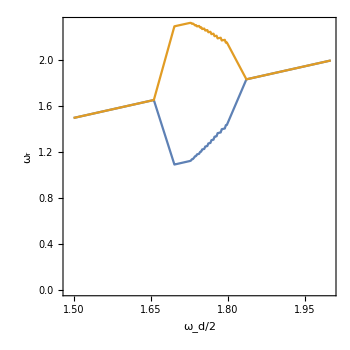
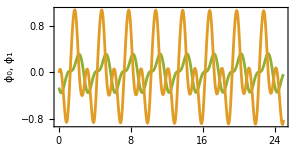
-Graphics- | -Graphics-
-Graphics-

fig2.pdf

```mathematica
filebase="data/anharmonic";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat1=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
filebase="data/noisy";
dat2=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];

Clear[t];
p1=ListPlot[{Transpose[{dt*Range[500],dat1[[-500;;-1,1]]}],Transpose[{dt*Range[500],dat1[[-500;;-1,2]]}]},PlotRange->All,Joined->True,Axes->False,Frame->True,PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]},FrameLabel->{DisplayForm[RowBox[{HoldForm[Subscript[ω,d]*t],"/",2π}]],DisplayForm[RowBox[{Style[Subscript[ϕ,0],ColorData[97,"ColorList"][[2]]],", ",Style[Subscript[ϕ,1],ColorData[97,"ColorList"][[3]]]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1/2];

n0=1000;
n2=Position[Differences[Sign[Differences[Total[Abs[#-dat1[[n0/dt]]]^2]&/@dat1]]],2][[-1,1]];
power1=Abs[Fourier[dat1[[n0/dt;;n2,1]]]];
freqs1=Range[Length[dat1[[n0/dt;;n2,1]]]]/(Length[dat1[[n0/dt+1;;n2,1]]]*dt);
power2=Abs[Fourier[dat2[[n0/dt;;n2,1]]]];
freqs2=Range[Length[dat2[[n0/dt;;n2,1]]]]/(Length[dat2[[n0/dt+1;;n2,1]]]*dt);
p2=Legended[rasterizeBackground[ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}]},PlotRange->{{0,1},{10^-3,10^2}},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]]},Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-3,2,2}],Table[{10^i,""},{i,-3,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1/2]],Placed[PointLegend[{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]]},{DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.,{2,1}]}]],DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.1,{2,1}]}]]},LabelStyle->Directive[13]],{0.82,0.7}]];
p0=Grid[{{p1},{p2}}];
p1=ListPlot[{{#[[1]]/2,#[[1]]*#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0&&u[[2]]==0.05],{#[[1]]/2,#[[1]]*(1-#[[4]])}&/@Cases[vals2,u_/;u[[3]]<0&&u[[2]]==0.05]},Joined->True,InterpolationOrder->1,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[ω,r]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ImagePadding->{{65,15},{65,10}},ImageSize->350];
p=Grid[{{p1,p0}}]
Export["fig2.pdf",p]
```

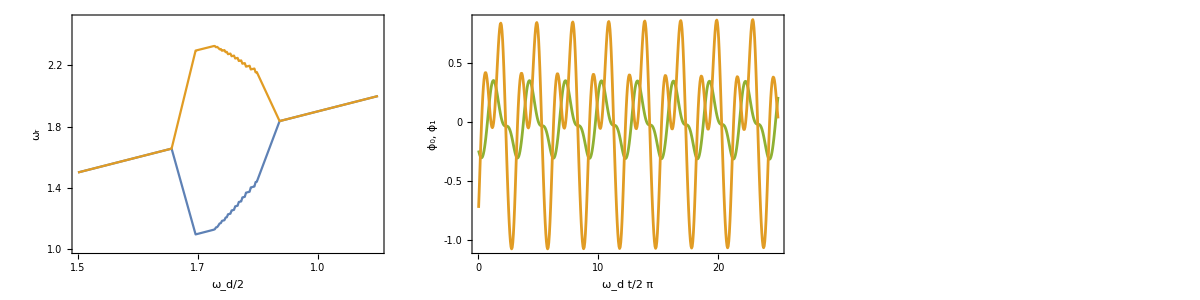

fig2.pdf

```mathematica
p1=ListPlot[{Transpose[{dt*Range[500],dat1[[-500;;-1,1]]}],Transpose[{dt*Range[500],dat1[[-500;;-1,2]]}]},PlotRange->All,Joined->True,Axes->False,Frame->True,PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]},FrameLabel->{DisplayForm[RowBox[{HoldForm[Subscript[ω,d]*t],"/",2π}]],DisplayForm[RowBox[{Style[Subscript[ϕ,0],ColorData[97,"ColorList"][[2]]],", ",Style[Subscript[ϕ,1],ColorData[97,"ColorList"][[3]]]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->2/3,FrameTicks->{{{{-1,PaddedForm[-1.,{2,1}]},{-0.5,PaddedForm[-0.5,{2,1}]},{0,PaddedForm[0,{2,1}]},{0.5,PaddedForm[0.5,{2,1}]},{1.0,PaddedForm[1.0,{2,1}]}},{{-1,""},{-0.5,""},{0,""},{0.5,""},{1.0,""}}},{{{0,0},{5,5},{10,10},{15,15},{20,20},{25,25}},{{0,""},{5,""},{10,""},{15,""},{20,""},{25,""}}}}];
p2=Legended[rasterizeBackground[ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}]},PlotRange->{{0,1},{10^-3,10^2}},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]]},Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-3,2,2}],Table[{10^i,""},{i,-3,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->2/3]],Placed[PointLegend[{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]]},{DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.,{2,1}]}]],DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.1,{2,1}]}]]},LabelStyle->Directive[13]],{0.82,0.7}]];
p3=ListPlot[{{#[[1]]/2,#[[1]]*#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0&&u[[2]]==0.05],{#[[1]]/2,#[[1]]*(1-#[[4]])}&/@Cases[vals2,u_/;u[[3]]<0&&u[[2]]==0.05]},Joined->True,InterpolationOrder->1,Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[ω,r]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300, AspectRatio->2/3,PlotRange->{{1.5,2.0},{1,2.5}},FrameTicks->{{{{1,PaddedForm[1.0,{2,1}]},{1.4,PaddedForm[1.4,{2,1}]},{1.8,PaddedForm[1.8,{2,1}]},{2.2,PaddedForm[2.2,{2,1}]}},{{1,""},{1.4,""},{1.8,""},{2.2,""}}},{{{1.5,PaddedForm[1.5,{2,1}]},{1.6,PaddedForm[1.6,{2,1}]},{1.7,PaddedForm[1.7,{2,1}]},{1.8,PaddedForm[1.8,{2,1}]},{1.9,PaddedForm[1.0,{2,1}]},{2.0,PaddedForm[2.0,{2,1}]}},{{1.5,""},{1.6,""},{1.7,""},{1.8,""},{1.9,""},{2.0,""}}}}];
p=Grid[{{p3,p1,p2}}]
Export["fig2.pdf",p]
```

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
cases1=Sort[DeleteDuplicates[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals1,u_/;u[[3]]<0])[[All,1]]]];
Monitor[boundary=Table[If[Length[Cases[vals1,u_/;u[[3]]<0&&u[[1]]==case]]>0,{case,MinimalBy[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals1,u_/;u[[3]]<0&&u[[1]]==case]),#[[2]]&][[1,2]]},{}],{case,cases1}];,case]
ac1=Interpolation[boundary];
cases2=Sort[DeleteDuplicates[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals2,u_/;u[[3]]<0])[[All,1]]]];
Monitor[boundary2=Table[If[Length[Cases[vals2,u_/;u[[3]]<0&&u[[1]]==case]]>0,{case,MinimalBy[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals2,u_/;u[[3]]<0&&u[[1]]==case]),#[[2]]&][[1,2]]},{}],{case,cases2}];,case]
ac2=Interpolation[boundary2];
min=0.3;
max=0.5;
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
Clear[ω]
;
```

InterpolatingFunction::dmval: Input value {0.800013} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.80003} lies outside the range of data in the interpolating function. Extrapolation will be used.

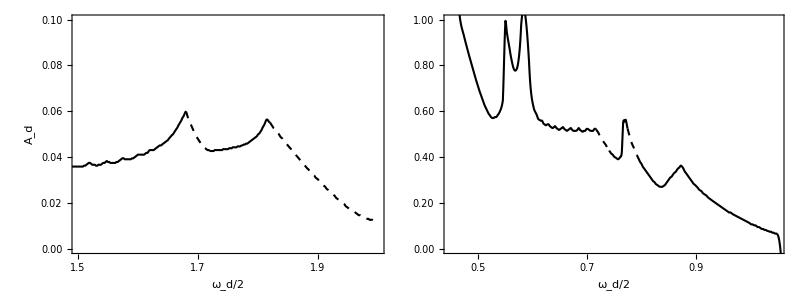

```mathematica
p1=Show[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3/2,0},{4/2,0},{4/2,0.1},{3/2,0.1},{3/2,0}}]},FrameTicks->{Transpose[{{#,PaddedForm[#,{2,2}]},{#,""}}&/@{0.0,0.2,0.4,0.6,0.8,1.0}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{0.5,0.6,0.7,0.8,0.9,1.0}]}]],Plot[ac1[2*ω]-0.005,{ω,1.55/2,1.584/2},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac1[2*ω]-0.005,{ω,1.434/2,1.482/2},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac1[2*ω]-0.005,{ω,1.584/2,2.5/2},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All],
Plot[ac1[2*ω]-0.005,{ω,0.8/2,1.434/2},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac1[2*ω]-0.005,{ω,1.482/2,1.55/2},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All]];
p2=Show[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{Transpose[{{#,PaddedForm[#,{2,2}]},{#,""}}&/@{0.0,0.02,0.04,0.06,0.08,0.10}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{1.5,1.6,1.7,1.8,1.9,2.0}]}]],Plot[ac2[2*ω]-0.0005,{ω,1.68,1.72},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]]],Plot[ac2[2*ω]-0.0005,{ω,1.82,2.0},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac2[2*ω]-0.0005,{ω,0.9,1.68},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac2[2*ω]-0.0005,{ω,1.72,1.82},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All]];
p=Legended[Grid[{{p2,p1}}],Placed[MatrixPlot[Table[cf[min+(max-min)*(j-1)/100],{j,1,100},{i,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,225},PlotLabel->ϵ,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
```

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
cases1=Sort[DeleteDuplicates[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals1,u_/;u[[3]]<0])[[All,1]]]];
Monitor[boundary=Table[If[Length[Cases[vals1,u_/;u[[3]]<0&&u[[1]]==case]]>0,{case,MinimalBy[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals1,u_/;u[[3]]<0&&u[[1]]==case]),#[[2]]&][[1,2]]},{}],{case,cases1}];,case]
ac1=Interpolation[boundary];
cases2=Sort[DeleteDuplicates[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals2,u_/;u[[3]]<0])[[All,1]]]];
Monitor[boundary2=Table[If[Length[Cases[vals2,u_/;u[[3]]<0&&u[[1]]==case]]>0,{case,MinimalBy[({#[[1]],#[[2]],#[[5]]}&/@Cases[vals2,u_/;u[[3]]<0&&u[[1]]==case]),#[[2]]&][[1,2]]},{}],{case,cases2}];,case]
ac2=Interpolation[boundary2];
min=0.3;
max=0.5;
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
Clear[ω]
p1=Show[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3/2,0},{4/2,0},{4/2,0.1},{3/2,0.1},{3/2,0}}]},FrameTicks->{Transpose[{{#,PaddedForm[#,{2,2}]},{#,""}}&/@{0.0,0.2,0.4,0.6,0.8,1.0}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{0.5,0.6,0.7,0.8,0.9,1.0}]}]],Plot[ac1[2*ω]-0.005,{ω,1.55/2,1.584/2},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac1[2*ω]-0.005,{ω,1.434/2,1.482/2},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac1[2*ω]-0.005,{ω,1.584/2,2.5/2},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All],
Plot[ac1[2*ω]-0.005,{ω,0.8/2,1.434/2},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac1[2*ω]-0.005,{ω,1.482/2,1.55/2},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All]];
p2=Show[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,1.01}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameTicks->{Transpose[{{#,PaddedForm[#,{2,2}]},{#,""}}&/@{0.0,0.02,0.04,0.06,0.08,0.10}],Transpose[{{#,PaddedForm[#,{2,1}]},{#,""}}&/@{1.5,1.6,1.7,1.8,1.9,2.0}]}]],Plot[ac2[2*ω]-0.0005,{ω,1.68,1.72},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]]],Plot[ac2[2*ω]-0.0005,{ω,1.82,2.0},PlotStyle->Directive[Dashed,Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac2[2*ω]-0.0005,{ω,0.9,1.68},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All],Plot[ac2[2*ω]-0.0005,{ω,1.72,1.82},PlotStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->All]];
p=Legended[Grid[{{p2,p1}}],Placed[MatrixPlot[Table[cf[min+(max-min)*(j-1)/100],{j,1,100},{i,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,225},PlotLabel->ϵ,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
Export["fig3.pdf",p]
```

InterpolatingFunction::dmval: Input value {0.800013} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.80003} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

fig3.pdf

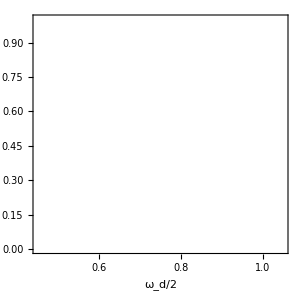
-Graphics- | -Graphics-

```mathematica
c1=Lighter[Blue];
c2=Lighter[Green];
min=0;
max=Pi;
cf[x_]:=Blend[{c1,c2},(x-min)/(max-min)]
Clear[ω]
p1=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,5}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,2*Pi}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],None},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3/2,0},{4/2,0},{4/2,0.1},{3/2,0.1},{3/2,0}}]}]];

p2=rasterizeBackground[Show[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[5]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,2*Pi}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]]];
p=Legended[Grid[{{p2,p1}}],Placed[MatrixPlot[Table[cf[min+(max-min)*(j-1)/100],{j,1,100},{i,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}},{None,None}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,225},PlotLabel->k,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
```

### Degenerate perturbation theory

```mathematica
vals3=Import["data/vals3.dat"];
c1=LightRed;
c2=Lighter[Cyan];
min=0;
max=Pi;
cf[x_]:=Blend[{c1,c2},(x-min)/(max-min)]
p2=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[5]]}&/@Cases[vals3,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals3,u_/;u[[3]]≥0]],PlotRange->{All,All,{-0.99,2*Pi}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,18],FrameStyle->Directive[Black,AbsoluteThickness[2]]]]
{evals,evecs}=Eigensystem[{{2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],2*κ+1/(1-Δ)}}];

Simplify[Transpose[evecs].{{1/(1+Δ),0},{0,1/(1-Δ)}}.Inverse[Transpose[evecs]]]
Simplify[(Δ (-1+Δ/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))))/(-1+Δ^2)*(Δ (-1-Δ/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))))/(-1+Δ^2)]
Simplify[(2 (-1+Δ) Δ Cos[q/2])/((1+Δ) √(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))*(2 Δ (1+Δ) Cos[q/2])/((-1+Δ) √(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))]
```

-Graphics-

{{-(1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2),(2 (-1+Δ) Δ Cos[q/2])/((1+Δ) √(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))},{(2 Δ (1+Δ) Cos[q/2])/((-1+Δ) √(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])),(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)}}

(4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])

(4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])

```mathematica
{evals[[2]]^(1/2),η/(2*(2*evals[[2]]^(1/2)))/(Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)}/.q->0/.Δ->0.5
{evals[[2]]^(1/2),η/(2*(2*evals[[2]]^(1/2)))/(Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)}/.q->Pi/.Δ->0.5
```

{1.10686,0.0402424}

{1.63299,0.0459279}

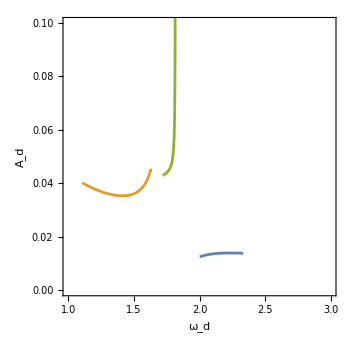

```mathematica
p1=ParametricPlot[Evaluate[{{evals[[1]]^(1/2),η/(2*(2*evals[[1]]^(1/2)))/(Abs[-(1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)},{evals[[2]]^(1/2),η/(2*(2*evals[[2]]^(1/2)))/(Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)},{(evals[[1]]^(1/2)+evals[[2]]^(1/2))/2,η/(2*(evals[[1]]^(1/2)+evals[[2]]^(1/2)))/(((4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))^(1/2)/(4*((evals[[1]]^(1/2)*evals[[2]]^(1/2))/(evals[[1]]^(1/2)+evals[[2]]^(1/2))^2)^(1/2)))}}/.Δ->0.5],{q,0,Pi-0.1},PlotRange->{{1.0,3.0},{0,0.1}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0.0,0.1,0.02}],Table[{i,""},{i,0.0,2.0,0.5}]},Automatic},Axes->False,Frame->True,FrameLabel->{Subscript[ω,d],Subscript[A,d]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,18],ImageSize->350,PlotStyle->Directive[AbsoluteThickness[2]],AspectRatio->1]
```

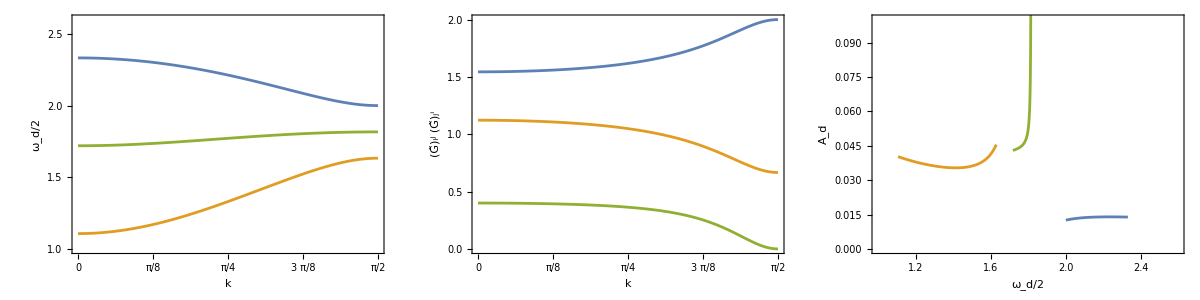

fig5.pdf

```mathematica
p1=ParametricPlot[Evaluate[{{evals[[1]]^(1/2),η/(2*(2*evals[[1]]^(1/2)))/(Abs[-(1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)},{evals[[2]]^(1/2),η/(2*(2*evals[[2]]^(1/2)))/(Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)},{(evals[[1]]^(1/2)+evals[[2]]^(1/2))/2,η/(2*(evals[[1]]^(1/2)+evals[[2]]^(1/2)))/(((4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))^(1/2)/(4*((evals[[1]]^(1/2)*evals[[2]]^(1/2))/(evals[[1]]^(1/2)+evals[[2]]^(1/2))^2)^(1/2)))}}/.Δ->0.5],{q,0,Pi-0.1},PlotRange->{{1.0,3.0},{0,0.1}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0.0,0.1,0.02}],Table[{i,""},{i,0.0,2.0,0.5}]},Automatic},Axes->False,Frame->True,FrameLabel->{Subscript[ω,d],Subscript[A,d]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,18],ImageSize->350,PlotStyle->Directive[AbsoluteThickness[2]],AspectRatio->1];
p3=Plot[Evaluate[{evals[[1]]^(1/2),evals[[2]]^(1/2),(evals[[1]]^(1/2)+evals[[2]]^(1/2))/2}/.Δ->0.5],{q,0,Pi},PlotRange->{1,2.6},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{Pi/4,DisplayForm[RowBox[{"π","/",8}]]},{Pi/2,DisplayForm[RowBox[{"π","/",4}]]},{3*Pi/4,DisplayForm[RowBox[{3"π","/",8}]]},{Pi,DisplayForm[RowBox[{"π","/",2}]]}},{{0,""},{Pi/4,""},{Pi/2,""},{3*Pi/4,""},{Pi,""}}}},Axes->False,Frame->True,FrameLabel->{k,DisplayForm[RowBox[{Subscript[ω,d],"/",2}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,18],ImageSize->300,ImagePadding->{{65,15},{65,10}},PlotStyle->Directive[AbsoluteThickness[2]],AspectRatio->1];
p4=ParametricPlot[Evaluate[{{q,Abs[-(1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]},{q,Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]},{q,(4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])}}/.Δ->0.5],{q,0,Pi},PlotRange->{{0,Pi},{0,2}},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.0,2.0,0.5}],Table[{i,""},{i,0.0,2.0,0.5}]},{{{0,0},{Pi/4,DisplayForm[RowBox[{"π","/",8}]]},{Pi/2,DisplayForm[RowBox[{"π","/",4}]]},{3*Pi/4,DisplayForm[RowBox[{3"π","/",8}]]},{Pi,DisplayForm[RowBox[{"π","/",2}]]}},{{0,""},{Pi/4,""},{Pi/2,""},{3*Pi/4,""},{Pi,""}}}},Axes->False,Frame->True,FrameLabel->{k,Subsuperscript[OverTilde[G],i,j]*Subsuperscript[OverTilde[G],j,i]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,18],ImageSize->300,ImagePadding->{{65,15},{65,10}},PlotStyle->Directive[AbsoluteThickness[2]],AspectRatio->1];
p=Legended[Grid[{{p3,p4,Show[p2,p1]}}],Placed[MatrixPlot[Table[cf[min+(max-min)*(j-1)/100],{j,1,100},{i,1,10}],PlotRangePadding->None,FrameTicks->{{None,{{1,0},{25,DisplayForm[RowBox[{Pi,"/",8}]]},{50,DisplayForm[RowBox[{Pi,"/",4}]]},{75,DisplayForm[RowBox[{3*Pi,"/",8}]]},{100,DisplayForm[RowBox[{Pi,"/",2}]]}}},{None,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->10,ImageSize->{Automatic,225},PlotLabel->k,PlotRange->{{1,100},{1,10}},DataReversed->{True,False}],Right]]
Export["fig5.pdf",p]
```

```mathematica
p1
Evaluate[{{evals[[1]]^(1/2),η/(2*(2*evals[[1]]^(1/2)))/(Abs[-((1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2))]/2)},{evals[[2]]^(1/2),η/(2*(2*evals[[2]]^(1/2)))/(Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)},{(evals[[1]]^(1/2)+evals[[2]]^(1/2))/2,η/(2*(evals[[1]]^(1/2)+evals[[2]]^(1/2)))/(((4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))^(1/2)/(4*((evals[[1]]^(1/2)*evals[[2]]^(1/2))/(evals[[1]]^(1/2)+evals[[2]]^(1/2))^2)^(1/2)))}}/.Δ->0.5]/.q->0
Evaluate[{{evals[[1]]^(1/2),η/(2*(2*evals[[1]]^(1/2)))/(Abs[-((1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2))]/2)},{evals[[2]]^(1/2),η/(2*(2*evals[[2]]^(1/2)))/(Abs[(-1+Δ^2/(√(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q])))/(-1+Δ^2)]/2)},{(evals[[1]]^(1/2)+evals[[2]]^(1/2))/2,η/(2*(evals[[1]]^(1/2)+evals[[2]]^(1/2)))/(((4 Δ^2 Cos[q/2]^2)/(2-3 Δ^2+2 Δ^4+2 (-1+Δ^2)^2 Cos[q]))^(1/2)/(4*((evals[[1]]^(1/2)*evals[[2]]^(1/2))/(evals[[1]]^(1/2)+evals[[2]]^(1/2))^2)^(1/2)))}}/.Δ->0.001]/.q->0
```

-Graphics-

{{2.33271,0.013881},{1.10686,0.0402424},{1.71979,0.0429506}}

{{2.23607,0.0223606},{1.,0.05},{1.61803,28.5586}}

```mathematica
1.7197851945526428*2
1.106864140965102*2
2.3327062481401835*2
```

3.43957

2.21373

4.66541

3.4379

{0.481946,Null}

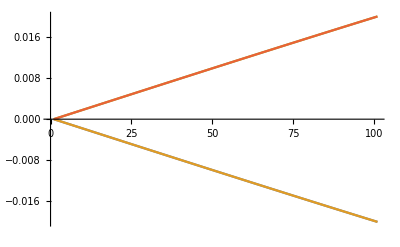

{0.11184,0.11184,0.11184,0.11184}

2.21147

{0.518254,Null}

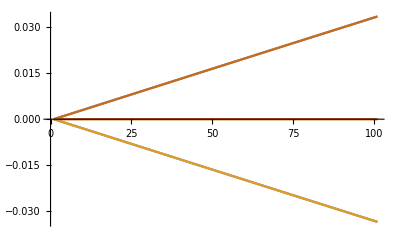

{0.313264,0.313264,1.22412×10^-29,5.94603×10^-29,0.313264,0.313264}

4.66434

{0.473777,Null}

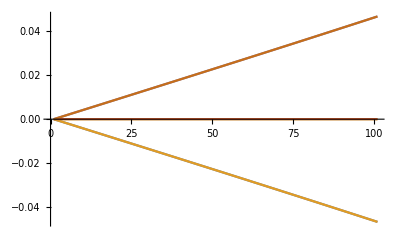

{0.608362,0.608362,4.3326×10^-31,7.83589×10^-32,0.608362,0.608362}

```mathematica
Δ=0.5;
q=0;
ωd=Re[#[[2]]+#[[4]]&@(ω/.dispersion/.q->0)]
amin=0.0;
amax=0.06;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51],{a,amin,amax,(amax-amin)/100}];],{a}]
ListPlot[Transpose[Sort/@Im[evals]-η/(2*ωd)],Joined->True]
D[Fit[#,{1,x},x]/((amax-amin)/100)&/@Transpose[Sort/@Im[evals]-η/(2*ωd)],x]^2

Δ=0.5;
q=0;
ωd=Re[2*#[[4]]&@(ω/.dispersion/.q->0)]
amin=0.0;
amax=0.06;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51],{a,amin,amax,(amax-amin)/100}];],{a}]
ListPlot[Transpose[Sort/@Im[evals]-η/(2*ωd)],Joined->True]
D[Fit[#,{1,x},x]/((amax-amin)/100)&/@Transpose[Sort/@Im[evals]-η/(2*ωd)],x]^2

Δ=0.5;
q=0;
ωd=Re[2*#[[2]]&@(ω/.dispersion/.q->0)]
amin=0.0;
amax=0.06;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51],{a,amin,amax,(amax-amin)/100}];],{a}]
ListPlot[Transpose[Sort/@Im[evals]-η/(2*ωd)],Joined->True]
D[Fit[#,{1,x},x]/((amax-amin)/100)&/@Transpose[Sort/@Im[evals]-η/(2*ωd)],x]^2
```

1.32942

0.664711

{0.528444,Null}

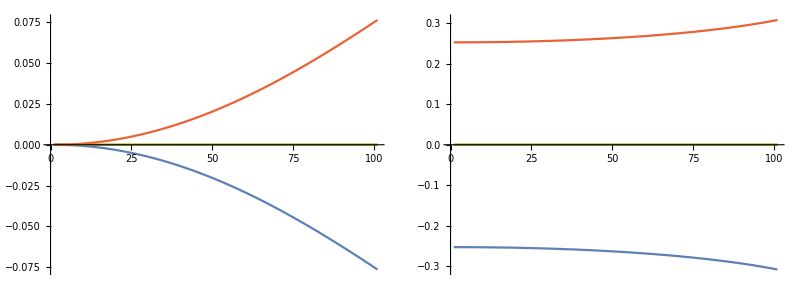

2.21231

1.10615

{0.527681,Null}

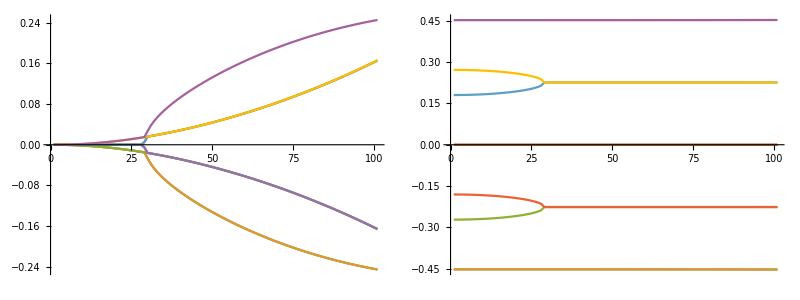

1.77086

0.885432

{0.502084,Null}

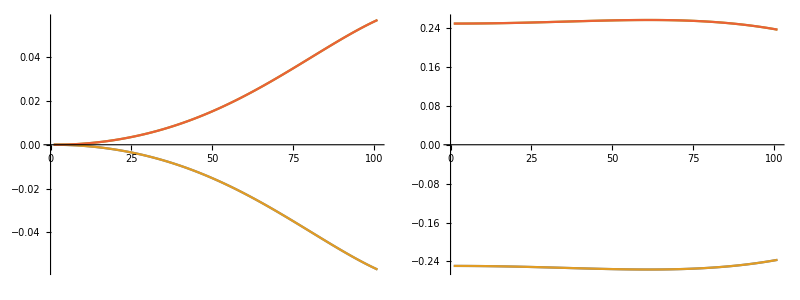

```mathematica
(* The low-frequency tongue is not a first-order perturbation result. It occurs for frequencies below resonance only. We could do an estimate of the amplitude needed to create degeneracy, then do an expansion of the imaginary part around that point.*)
Δ=0.5;
q=Pi/2;
ωd=Re[#[[4]]&@(ω/.dispersion)]
ωd/2
amin=0.0;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];

Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51],{a,amin,amax,(amax-amin)/100}];],{a}]
Grid[{{ListPlot[Transpose[Sort/@Im[evals]-η/(2*ωd)],Joined->True,PlotRange->All,ImageSize->350],ListPlot[Transpose[Sort/@Re[evals]/ωd],Joined->True,PlotRange->All,ImageSize->350]}}]
Δ=0.5;
q=Pi/2;
ωd=Re[#[[2]]&@(ω/.dispersion)]
ωd/2
amin=0.0;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];

Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-1.1&&Re[u]<1.1],{a,amin,amax,(amax-amin)/100}];],{a}]
Grid[{{ListPlot[Transpose[(Sort/@Im[evals]-η/(2*ωd))[[All,1;;9]]],Joined->True,PlotRange->All,ImageSize->350],ListPlot[Transpose[(Sort/@Re[evals]/ωd)[[All,1;;9]]],Joined->True,PlotRange->All,ImageSize->350]}}]

Δ=0.5;
q=Pi/2;
ωd=Re[(#[[2]]+#[[4]])/2&@(ω/.dispersion)]
ωd/2
amin=0.0;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];

Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51],{a,amin,amax,(amax-amin)/100}];],{a}]
Grid[{{ListPlot[Transpose[(Sort/@Im[evals]-η/(2*ωd))],Joined->True,PlotRange->All,ImageSize->350],ListPlot[Transpose[(Sort/@Re[evals])],Joined->True,PlotRange->All,ImageSize->350]}}]
```

1.10573

0.552867

{0.478187,Null}

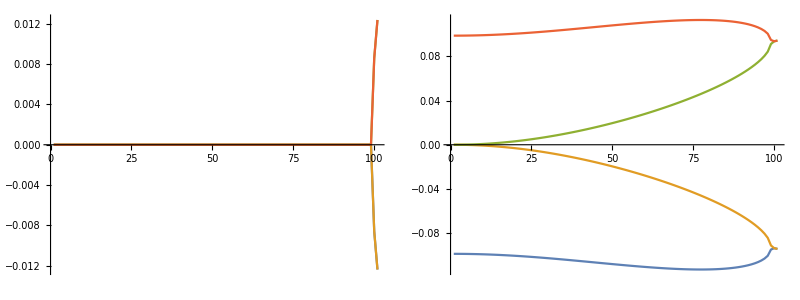

2.33217

1.16609

{0.464796,Null}

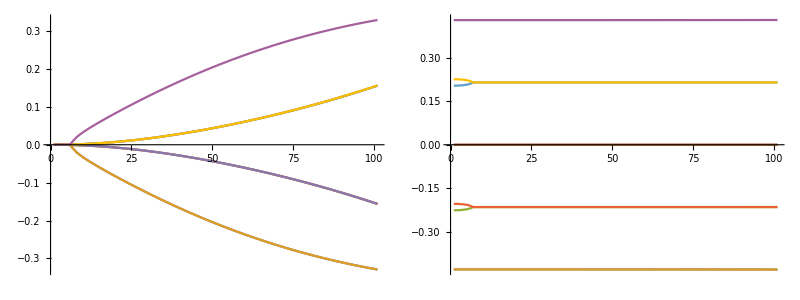

1.71895

0.859476

{0.475282,Null}

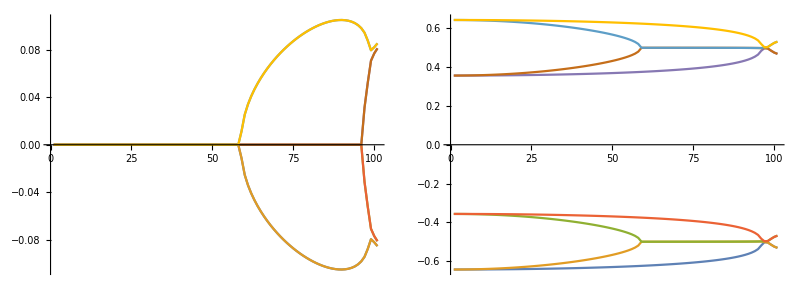

```mathematica
(* The low-frequency tongue is not a first-order perturbation result. It occurs for frequencies below resonance only. We could do an estimate of the amplitude needed to create degeneracy, then do an expansion of the imaginary part around that point.*)
Δ=0.5;
q=0;
ωd=Re[#[[4]]&@(ω/.dispersion)]
ωd/2
amin=0.0;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];

Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51],{a,amin,amax,(amax-amin)/100}];],{a}]
Grid[{{ListPlot[Transpose[Sort/@Im[evals]-η/(2*ωd)],Joined->True,PlotRange->All,ImageSize->350],ListPlot[Transpose[Sort/@Re[evals]/ωd],Joined->True,PlotRange->All,ImageSize->350]}}]
Δ=0.5;
q=0;
ωd=Re[#[[2]]&@(ω/.dispersion)]
ωd/2
amin=0.0;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];

Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-1.1&&Re[u]<1.1],{a,amin,amax,(amax-amin)/100}];],{a}]
Grid[{{ListPlot[Transpose[(Sort/@Im[evals]-η/(2*ωd))[[All,1;;9]]],Joined->True,PlotRange->All,ImageSize->350],ListPlot[Transpose[(Sort/@Re[evals]/ωd)[[All,1;;9]]],Joined->True,PlotRange->All,ImageSize->350]}}]

Δ=0.5;
q=0;
ωd=Re[(#[[2]]+#[[4]])/2&@(ω/.dispersion)]
ωd/2
amin=0.0;
amax=0.8;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-1.1&&Re[u]<1.1];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-1.1&&Re[u]<1.1];

Monitor[AbsoluteTiming[evals=Table[
Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-1.1&&Re[u]<1.1],{a,amin,amax,(amax-amin)/100}];],{a}]
Grid[{{ListPlot[Transpose[(Sort/@Im[evals]-η/(2*ωd))[[All,1;;8]]],Joined->True,PlotRange->All,ImageSize->350],ListPlot[Transpose[(Sort/@Re[evals])[[All,1;;8]]],Joined->True,PlotRange->All,ImageSize->350]}}]
```

```mathematica
N[18/16]
```

1.125

## Animations

### harmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/harmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals1.dat"];
amin=0.01;
evals1=SortBy[Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
evals2=SortBy[Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
count=0;
n0=Max[1,Length[dat]-499];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
Clear[ω]
p2=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{"Driving frequency", "(",Subscript[ω,d],"/",2,")"}]],DisplayForm[RowBox[{"Driving amplitude", "(",Subscript[A,d],")"}]]},LabelStyle->Directive[Black,18],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]];
```

{32,1.,0.8,0.05,0.1,0.,0.5,5000.,1,1}

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<150,amin+(amax-amin)/150*(n-n0),amax];
evals=SortBy[Cases[Eigenvalues[{A[a,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[1]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[1]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
```

{4.7532,Null}

{9.22033,Null}

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

/Users/zack/Documents/oscillators/anharmonic/data/harmonicanimation/1/

/Users/zack/Documents/oscillators/anharmonic/data/harmonicanimation/4/

{90.5756,Null}

{65.6084,Null}

{69.79,Null}

{33.483,Null}

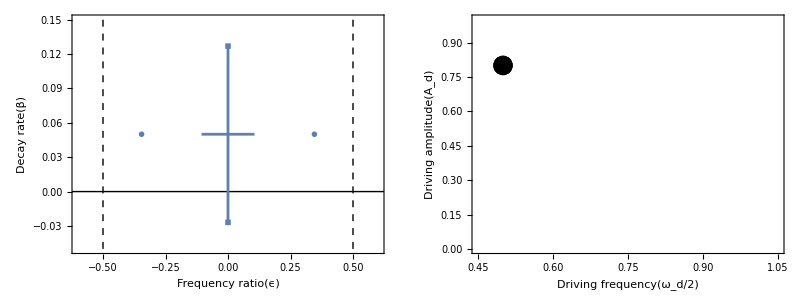

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots2=Table[
a=If[(n-n0)<150,amin+(amax-amin)/150*(n-n0),amax];
evals=SortBy[Cases[Eigenvalues[{A[a,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5],Re[#]&];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[{1,4}]],{Re[#],ωd*Im[#]}&/@evals[[{2,3}]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{"Frequency ratio", "(",ϵ,")"}]],DisplayForm[RowBox[{"Decay rate", "(",β,")"}]]},LabelStyle->Directive[Black,18],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.08]],PlotMarkers->{Graphics[{Disk[{0,0},0.05]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{{-1,1},{-1,1}}]},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
a=If[(n-n0)<150,amin+(amax-amin)/150*(n-n0),amax];
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[Black,PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Grid[{{plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
```

{20.0062,Null}

{26.1307,Null}

### subharmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/subharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/valss.dat"];
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
count=0;
n0=Max[1,Length[dat]-499];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
p2=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{"Driving frequency", "(",Subscript[ω,d],"/",2,")"}]],DisplayForm[RowBox[{"Driving amplitude", "(",Subscript[A,d],")"}]]},LabelStyle->Directive[Black,18],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]]
```

{32,2.,0.12,0.05,0.1,0.,0.5,5000.,1,1}

-Graphics-

{3.84589,Null}

{15.2633,Null}

{8.24749,Null}

{31.0876,Null}

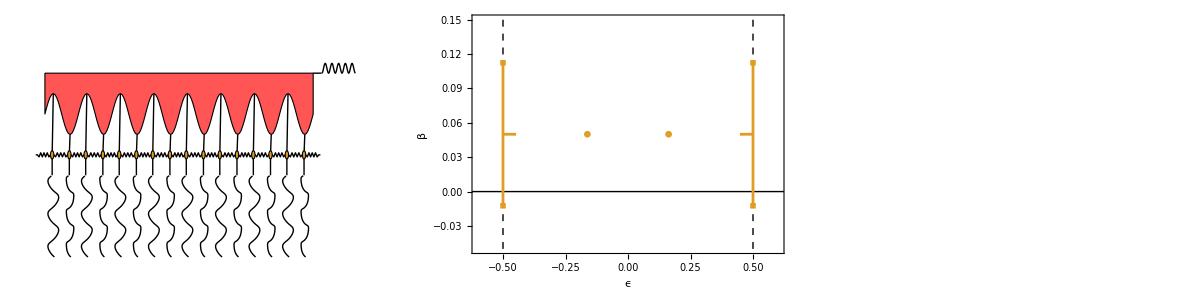

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count=Round[(n-n0)/20];
count2=Round[(n-n0)/40];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p1=Show[ListPlot[If[Length[evals]<6,{{Re[#],ωd*Im[#]}&/@evals[[{3,4}]],{Re[#],ωd*Im[#]}&/@evals[[{1,2}]]},{{Re[#],ωd*Im[#]}&/@evals[[5;;6]],{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]}],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.08]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

{13.5293,Null}

{4.32614,Null}

{12.1001,Null}

{66.6763,Null}

{44.0354,Null}

{8.68951,Null}

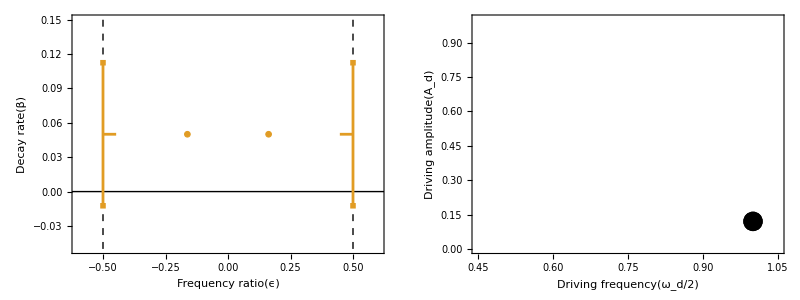

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots2=Table[
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[If[Length[evals]<6,{{Re[#],ωd*Im[#]}&/@evals[[{3,4}]],{Re[#],ωd*Im[#]}&/@evals[[{1,2}]]},{{Re[#],ωd*Im[#]}&/@evals[[5;;6]],{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]}],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{"Frequency ratio", "(",ϵ,")"}]],DisplayForm[RowBox[{"Decay rate", "(",β,")"}]]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.08]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{{-1,1},{-1,1}}]},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[Black,PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
Grid[{{plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
```

/Users/zack/Documents/oscillators/anharmonic/data/subharmonicanimation/3/

{37.3524,Null}

{39.3118,Null}

### anharmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/anharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals2.dat"];
amin=0.01;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
p2=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,0.1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{"Driving frequency", "(",Subscript[ω,d],"/",2,")"}]],DisplayForm[RowBox[{"Driving amplitude", "(",Subscript[A,d],")"}]]},LabelStyle->Directive[Black,18],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]]
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

-Graphics-

{20.0822,Null}

{76.0472,Null}

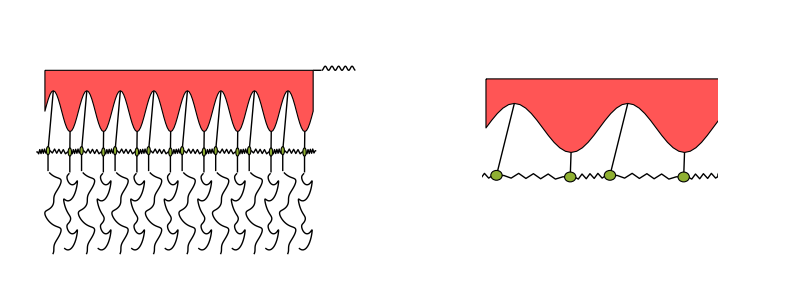

```mathematica
n0=Max[1,Length[dat]-1500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count=Round[(n-n0)/20];
count2=Round[(n-n0)/40];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots1[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

/Users/zack/Documents/oscillators/anharmonic/data/anharmonicanimation/1/

/Users/zack/Documents/oscillators/anharmonic/data/anharmonicanimation/4/

{260.362,Null}

{332.026,Null}

{33.6629,Null}

{17.711,Null}

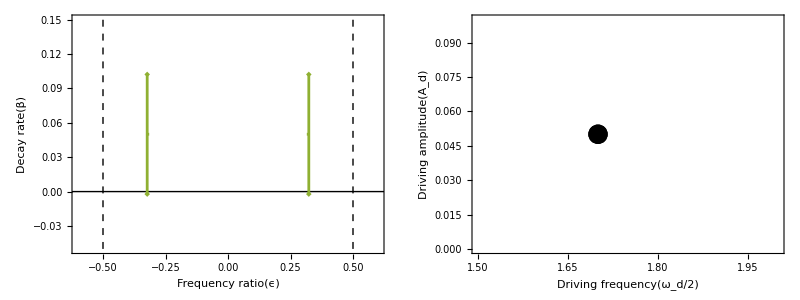

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots2=Table[
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{"Frequency ratio", "(",ϵ,")"}]],DisplayForm[RowBox[{"Decay rate", "(",β,")"}]]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.08]],PlotMarkers->If[Abs[#[[1]]-#[[2]]]<10^-6&@Abs[Re[evals[[{1,3}]]]],{Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{{-1,1},{-1,1}}]},{Graphics[{Disk[{0,0},0.05]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{{-1,1},{-1,1}}]}],ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[Black,PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
Grid[{{plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
```

/Users/zack/Documents/oscillators/anharmonic/data/anharmonicanimation/3/

{37.1913,Null}

{40.4975,Null}

### anharmonic2

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/anharmonic2";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals=Import["data/vals1.dat"];
amin=0.01;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
c1=Lighter[Magenta];
c2=Lighter[Orange];
c3=Lighter[Cyan];
c4=Lighter[Red];
min=0.32;
max=0.42;
cf[x_]:=Piecewise[{{White,x<-0.01},{c3,x<min},{c4,x>max},{Blend[{c1,c2},(x-min)/(max-min)],True}}]
p2=rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,4}]]&/@Cases[vals,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{-0.1,1.0}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{"Driving frequency", "(",Subscript[ω,d],"/",2,")"}]],DisplayForm[RowBox[{"Driving amplitude", "(",Subscript[A,d],")"}]]},LabelStyle->Directive[Black,18],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]]
```

{32,1.6,0.4,0.05,0.1,0.,0.5,5000.,1,1}

-Graphics-

{4.41285,Null}

{17.8939,Null}

{15.4222,Null}

{39.1603,Null}

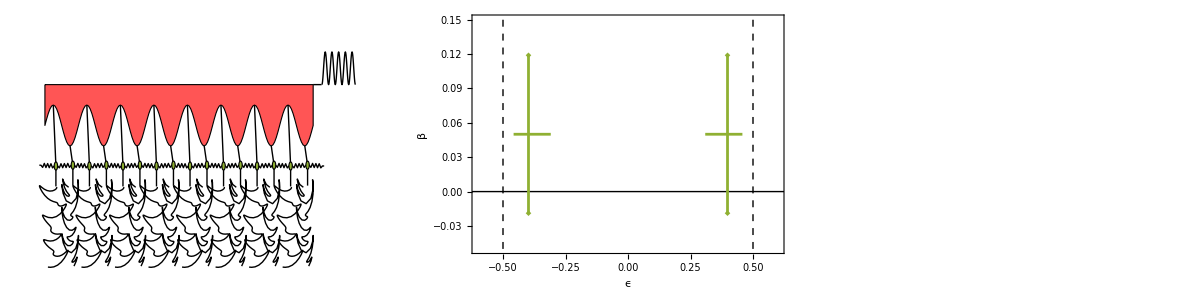

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
count=Round[(n-n0)/20];
count2=Round[(n-n0)/40];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],White, Text[Style[ToString[count]<>" driving periods  "<>ToString[count2]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};

evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.08]],PlotMarkers->If[Abs[#[[1]]-#[[2]]]<10^-6&@Abs[Re[evals[[{1,3}]]]],{Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}]},{Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]}],ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,-a*Cos[ωd*t]};
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
n0=Max[1,Length[dat]-2500];
Clear[a];
Clear[t];
Clear[m]
M=16;
Monitor[AbsoluteTiming[plots4=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a[m_]:=amax;
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=ωd*t[m-n0];
thetas=dat[[n,1;;M]];
thetas2=dat[[n-100;;n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]}}],{i,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas2[[101-m,i]]],Cos[thetas2[[101-m,i]]]}-{0,0.02*m},{m,1,100}]],{i,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p0}]
Grid[{{plots4[[-1]],plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
If[!DirectoryQ[filebase<>"animation/4/"],CreateDirectory[filebase<>"animation/4/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/4/"<>IntegerString[n,10,4]<>".png",plots4[[n]]], {n,1,Length[plots4]}]]
```

{18.1243,Null}

{4.02079,Null}

{14.5961,Null}

{66.3075,Null}

{40.9973,Null}

{28.3426,Null}

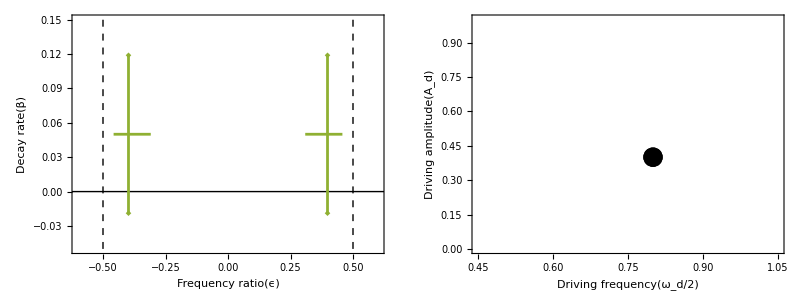

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots2=Table[
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{DisplayForm[RowBox[{"Frequency ratio", "(",ϵ,")"}]],DisplayForm[RowBox[{"Decay rate", "(",β,")"}]]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.08]],PlotMarkers->If[Abs[#[[1]]-#[[2]]]<10^-6&@Abs[Re[evals[[{1,3}]]]],{Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{{-1,1},{-1,1}}]},{Graphics[{Disk[{0,0},0.05]},PlotRange->{{-1,1},{-1,1}}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{{-1,1},{-1,1}}]}],ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p1}]
Monitor[AbsoluteTiming[plots3=Table[
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
p3=Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[Black,PointSize[0.04]]]],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p3}]
Grid[{{plots2[[-1]],plots3[[-1]]}}]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
If[!DirectoryQ[filebase<>"animation/3/"],CreateDirectory[filebase<>"animation/3/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/3/"<>IntegerString[n,10,4]<>".png",plots3[[n]]], {n,1,Length[plots3]}]]
```

/Users/zack/Documents/oscillators/anharmonic/data/anharmonic2animation/2/

/Users/zack/Documents/oscillators/anharmonic/data/anharmonic2animation/3/

{37.7286,Null}

{41.3945,Null}

### subharmonic2

{32,2.,0.15,0.05,0.1,0.,0.5,1000.,1,1}

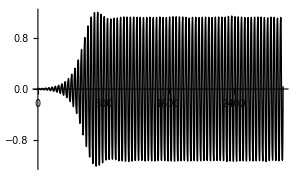

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/subharmonic2";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
ω1=ωd/2;
ω2=ωd;
n0=101;
M=16;
frames=3000;
response=dat[[n0;;n0+frames,2]];
ListPlot[response,ImageSize->300,Joined->True,Axes->{False,True},PlotRange->All]
```

{52.4982,Null}

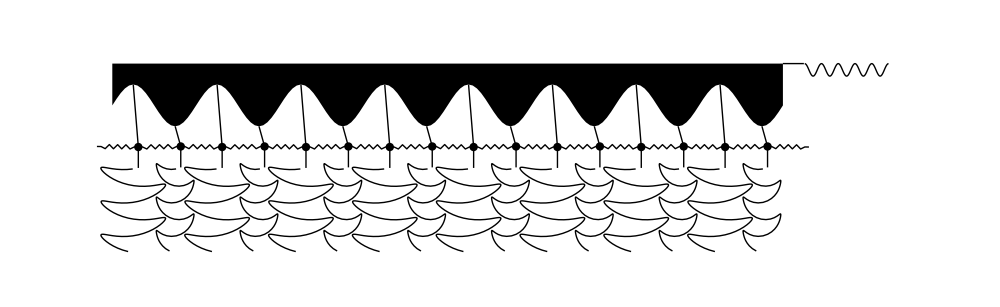

```mathematica
Monitor[AbsoluteTiming[plots=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
a[m_]:=Piecewise[{{amin,(m-n0)<frames/5},{amin+(amax-amin)/(frames/5)*(m-n0-frames/5),(m-n0)<frames*2/5},{amax, True}}];
t[m_]:=2*Pi*0.05/ωd*m;
θ[m_]:=Piecewise[{{ω1*t[m-n0],(m-n0)≤ frames*2/5},{ω1*t[m-n0]+1/2*(ω2-ω1)*(t[m-n0]-t[2*frames/5])^2/(t[3*frames/5]-t[2*frames/5]),(m-n0)≤ 3*frames/5},{ω2*t[m-n0]-(ω2-ω1)*(t[3*frames/5]+t[2*frames/5])/2, True}}];
thetas=If[(n-n0)<3*frames/5,ConstantArray[0,M],dat[[n0+n-3*frames/5,1;;M]]];
thetas2=Table[If[(m-n0)<3*frames/5,ConstantArray[0,M],dat[[n0+m-3*frames/5,1;;M]]],{m,n-100,n}];
f[x_]:=-delta*Cos[Pi*x/dx];
z0={0,-a[n]*Cos[θ[n]-θ[n0]]};
p=Graphics[{Black, 
Table[Line[{z0+{dx*n,1+lengths[[n]]} -(1+ lengths[[n]])*{Sin[thetas[[n]]],Cos[thetas[[n]]]},{0,-1/2}+z0+{dx*n,1+lengths[[n]]} -(1+ lengths[[n]])*{Sin[thetas[[n]]],Cos[thetas[[n]]]}}],{n,1,M}],
Table[Line[Table[{0,-1/2}+z0+{dx*n,1+lengths[[n]]} -(1+ lengths[[n]])*{Sin[thetas2[[101-m,n]]],Cos[thetas2[[101-m,n]]]}-{0,0.02*m},{m,1,100}]],{n,1,M}],

Line[{{dx*(M+1/2),z0[[2]]+2},{0.5+dx*(M+1/2),z0[[2]]+2}}],
Line[{0.5+dx*(M+1/2),2}+#&/@Transpose[{0.02*Range[101],Reverse[Table[-a[m]*Cos[θ[m]],{m,n-100,n,1}]]}]],

Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->1000,PlotRange->{-1/2+dx*{1/2,M+3.5+1/2},{-3,3}}],{n,n0,n0+frames}];],{PaddedForm[N[(n-n0)/frames],{3,3}],p}]
plots[[-1]]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots[[n]]], {n,1,Length[plots]}]]
```

{83.2426,Null}

-Graphics-

1.25144

-Graphics- | -Graphics- | -Graphics-

Power::infy: Infinite expression 1/0. encountered.

{ComplexInfinity,40}

Part::span: ComplexInfinity;;-1 is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

80

Part::span: Indeterminate;;-1;;ComplexInfinity is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{ComplexInfinity},Log[{4.5679×10^-6,5.3525×10^-6,3.33994×10^-6,4.33849×10^-6,«43»,3.13093×10^-7,1.77833×10^-7,3.99347×10^-7,«39950»}⟦«13»;;«1»;;«15»⟧]/Log[10]} cannot be transposed.

Transpose::nmtx: The first two levels of {{ComplexInfinity},0.4342944819032518 Log[{4.5679×10^-6,5.3525×10^-6,3.33994×10^-6,4.33849×10^-6,2.9113×10^-6,3.53622×10^-6,3.10179×10^-6,«37»,1.93432×10^-7,4.18289×10^-7,3.52782×10^-7,3.13093×10^-7,1.77833×10^-7,3.99347×10^-7,«39950»}⟦Indeterminate;;-1;;«15»⟧]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

-Graphics- | -Graphics-

Part::span: 1;;-1;;ComplexInfinity is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Divide::indet: Indeterminate expression 0./0. encountered.

Table::iterb: Iterator {i,0,0.,0.} does not have appropriate bounds.

Divide::indet: Indeterminate expression 0./0. encountered.

Table::iterb: Iterator {i,0,0.,0.} does not have appropriate bounds.

Divide::indet: Indeterminate expression 0./0. encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Table::iterb: Iterator {i,0,0.,0.} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListDensityPlot::arrayerr: {{-0.000337899,-0.00231168,-0.000256053,-0.000494616,-0.000471345,-0.00172754,-0.00107312,-0.000681416,-0.000788927,«34»,0.000321241,0.0000710794,-0.000323036,-0.0000526473,0.00134624,0.000688655,0.00238522,«1950»},«49»,«39950»}⟦«1»,«1»⟧ must be a valid array.